```mathematica
Quit[]
```

```mathematica
Vertices[data_,centre_]:=Map[#-centre &,Cases[data,{"v",x_,y_,z_}-> {x,y,z}]]
```

```mathematica
Atlas=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/Atlas.obj","BoundaryMeshRegion"(*"GraphicsComplex"*)];
Lutetia=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/21Lutetia.obj","BoundaryMeshRegion"(*"GraphicsComplex"*)];
Kleopatra=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/216Kleopatra.obj"(*"GraphicsComplex"*)];

dataAtlas=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/Atlas.obj","Table"];
dataLutetia=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/21Lutetia.obj","Table"];
dataKleopatra=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/216Kleopatra.obj","Table"];
```

```mathematica
{Graphics3D[Atlas,Boxed->False],Graphics3D[Lutetia,Boxed->False],Graphics3D[Kleopatra,Boxed->False]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*matCentre={{RegionCentroid[Lutetia], Volume[Lutetia], Area[RegionBoundary[Lutetia]]},{RegionCentroid[Atlas], Volume[Atlas], Area[RegionBoundary[Atlas]]},{RegionCentroid[Kleopatra], Volume[Kleopatra], Area[RegionBoundary[Kleopatra]]}}//MatrixForm*)
```

```mathematica
{centreLutetia,centreAtlas,centreKleopatra}={RegionCentroid[Lutetia],RegionCentroid[Atlas],RegionCentroid[Kleopatra]}
```

{{1.61516,2.69139,0.94739},{-0.0687444,-0.0167443,-0.0472993},{0.545271,-0.0145182,-0.531176}}

```mathematica
{verLutetia,verAtlas,verKleopatra}={Vertices[dataLutetia,centreLutetia],Vertices[dataAtlas,centreAtlas],Vertices[dataKleopatra,centreKleopatra]};
```

```mathematica
Cases[dataLutetia,{"v",x_,y_,z_}-> {x,y,z}]
```

{{-27.9254,31.4453,22.3294},{-21.7449,29.8663,25.5353},{-15.2757,30.0557,25.3183},{-12.7678,27.5311,27.2375},{-11.7445,31.5965,24.1371},{-8.3911,29.4562,25.9531},{-7.27086,33.001,23.5596},1469,{22.3742,30.4683,-34.2976},{8.37409,32.1765,-35.465},{-27.8957,28.2956,-29.12},{-6.49115,32.1997,-32.9579},{-24.8526,31.6232,-28.989},{15.0984,34.6577,-33.5157},{5.14799,35.292,-33.4047}}
 |  |  |  |

```mathematica
centreLutetia
```

{1.61516,2.69139,0.94739}

```mathematica
verLutetia
```

{{-29.5405,28.7539,21.382},{-23.36,27.1749,24.5879},{-16.8909,27.3643,24.3709},{-14.383,24.8397,26.2901},1475,{-8.10631,29.5083,-33.9053},{-26.4678,28.9319,-29.9364},{13.4832,31.9663,-34.4631},{3.53283,32.6006,-34.3521}}
 |  |  |  |

```mathematica
{coordSphLutetia,coordSphAtlas,coordSphKleopatra}={ToSphericalCoordinates[verLutetia],ToSphericalCoordinates[verAtlas],ToSphericalCoordinates[verKleopatra]};
```

```mathematica
coordSphTrAtlas=FromSphericalCoordinates[coordSphAtlas];
```

```mathematica
ListPlot3D[coordSphTrAtlas];
```

```mathematica
{{rLutetia,θLutetia,ϕLutetia},{rAtlas,θAtlas,ϕAtlas},{rKleopatra,θKleopatra,ϕKleopatra}}={Transpose[coordSphLutetia],Transpose[coordSphAtlas],Transpose[coordSphKleopatra]};
```

```mathematica
{coordFitLutetia,coordFitAtlas,coordFitKleopatra}={Transpose[{θLutetia,ϕLutetia,rLutetia}],Transpose[{θAtlas,ϕAtlas,rAtlas}],Transpose[{θKleopatra,ϕKleopatra,rKleopatra}]};
```

```mathematica
coordFitLutetia[[1;;2]]
```

{{1.09232,2.36969,46.4395},{0.969436,2.28085,43.4595}}

```mathematica
coordSphLutetia[[1;;2]]
```

{{46.4395,1.09232,2.36969},{43.4595,0.969436,2.28085}}

```mathematica
SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
√((2l+1)/(2π)((l-m)!)/((l+m)!))LegendreP[l,m,Cos[θ]]Sin[m ϕ]
```

```mathematica
(-1)^-m √((2l+1)/(2π)((l-m)!)/((l+m)!))LegendreP[l,m,Cos[θ]]Cos[-m ϕ]
```

```mathematica
1-Cos[x]^2//TrigReduce
```

1/2 (1-Cos[2 x])

```mathematica
Quit[]
```

ClearAll

```mathematica
lMax=2;
```

```mathematica
formFit=Flatten[Table[Table[If[m<0,(-1)^m √((2l+1)/(2π)((l-Abs[m])!)/((l+Abs[m])!))LegendreP[l,Abs[m],Cos[θ]]Sin[Abs[m] ϕ],If[m==0,√((2l+1)/(4π))LegendreP[l,m,Cos[θ]],(-1)^m √((2l+1)/(2π)((l-m)!)/((l+m)!))LegendreP[l,m,Cos[θ]]Cos[m ϕ]]],{m,-l,l}],{l,0,lMax}]]
```

{1/(2 √π),1/2 √(3/π) √(1-Cos[θ]^2) Sin[ϕ],1/2 √(3/π) Cos[θ],1/2 √(3/π) √(1-Cos[θ]^2) Cos[ϕ]}

```mathematica
rLinLutetia=LinearModelFit[coordFitLutetia,formFit,{θ,ϕ}]
```

FittedModel[50.0671+0.155186 Cos[θ]-0.147073 √(1-Cos[θ]^2) Cos[ϕ]-0.24497 √(1-Cos[θ]^2) Sin[ϕ]]

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},rLinLutetia[θ,ϕ]//Simplify]
```

50.0671+0.155186 Cos[θ]-0.147073 Cos[ϕ] Sin[θ]-0.24497 Sin[θ] Sin[ϕ]

l_max=2

```mathematica
rFitLutetia[θ_,ϕ_]:=50.067111118223465+0.15518593969077757 Cos[θ]-0.14707320958048292 Cos[ϕ] Sin[θ]-0.2449695081581425 Sin[θ] Sin[ϕ]
```

l_max=5

```mathematica
rFitLutetia[θ_,ϕ_]:=54.348611211485164-1.4425591445501287 Cos[4 ϕ]-2.209429381828982 Cos[ϕ] Sin[θ]+2.818318784549385 Cos[3 ϕ] Sin[θ]^3+0.5926815015846589 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.5485234942542312-1.450342390847195 Sin[θ]^2)+10.792514116115738 Cos[ϕ] Sin[ϕ]+0.310776231872863 Sin[θ] Sin[ϕ]+0.34963231611902584 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.09501125348435324 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.816394486903914-1.4425591445501287 Cos[4 ϕ]-9.87471576073588 Cos[ϕ] Sin[θ]+8.262904985870692 Sin[θ] Sin[ϕ]-0.7105735562332913 Sin[4 ϕ])+Cos[θ]^5 (8.162834015917953-1.8501410274585612 Cos[4 ϕ]-0.6536043000716671 Sin[4 ϕ])+Cos[θ] (-0.8294685911214945-1.8501410274585612 Cos[4 ϕ]-0.6949134283251226 Cos[ϕ] Sin[θ]-3.4232932422692173 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.2553780488396649-2.552641824321018 Sin[θ]^2)-0.04496785438214449 Cos[ϕ] Sin[ϕ]+5.076578690838504 Sin[θ] Sin[ϕ]-0.44401242319781603 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8363977427433156 Sin[θ]^3 Sin[3 ϕ]-0.6536043000716671 Sin[4 ϕ])-0.7105735562332913 Sin[4 ϕ]+Cos[θ]^3 (-3.829203361665252+3.7002820549171225 Cos[4 ϕ]+5.701583504162247 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.2553780488396649+7.657925472963054 Sin[θ]^2)+0.04496785438214449 Cos[ϕ] Sin[ϕ]-13.26738416110994 Sin[θ] Sin[ϕ]+1.3320372695934481 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.3072086001433343 Sin[4 ϕ])+Cos[θ]^2 (-20.84443005322268+2.8851182891002574 Cos[4 ϕ]+17.870930309173815 Cos[ϕ] Sin[θ]+0.7477290031628104 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.5485234942542312+10.152396735930365 Sin[θ]^2)-10.792514116115738 Cos[ϕ] Sin[ϕ]-2.1813831855957346 Sin[θ] Sin[ϕ]-2.447426212833181 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.946030327967996 Sin[θ]^3 Sin[3 ϕ]+1.4211471124665827 Sin[4 ϕ])+1.1725246339950335 Sin[θ]^5 Sin[5 ϕ]
```

```mathematica
Interpreter["Color"]["light brown"]
```

RGBColor[0.7333333333333333, 0.6, 0.4666666666666667]

```mathematica
plot3DFitLutetia=SphericalPlot3D[rFitLutetia[θ,ϕ],{θ,0,π},{ϕ,-π,π},PlotStyle->RGBColor[0.7333333333333333, 0.6, 0.4666666666666667]]
```

-Graphics3D-

```mathematica
plotFitLutetia=Show[{plot3DFitLutetia,Graphics3D[{Yellow,Opacity[0.5],Lutetia}]}]
```

-Graphics3D-

```mathematica
dataErrorL15=Map[100 Abs[(rFitLutetia[#[[1]],#[[2]]]-#[[3]])/(#[[3]])]&,coordFitLutetia];
```

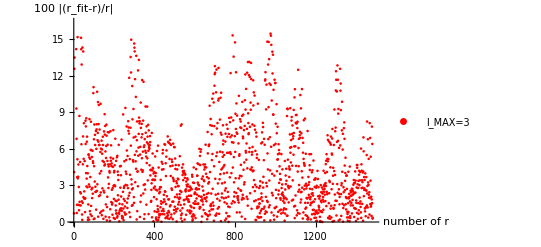

```mathematica
plotErrL3=ListPlot[Transpose[{Range[dataErrorL3//Length],dataErrorL3}],PlotStyle->Red,AxesLabel->{Style["number\n of r",FontFamily->"Times",Medium],Style["100 |(r_fit-r)/r|",FontFamily->"Times",Medium]},PlotLegends->{Style["l_MAX=3",FontFamily->"Times"]}]
```

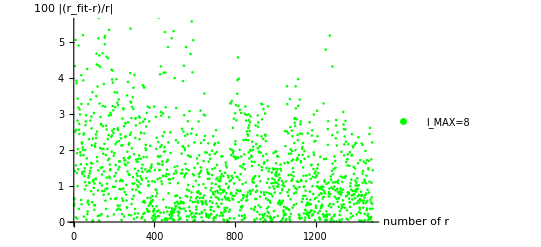

```mathematica
plotErrL8=ListPlot[Transpose[{Range[dataErrorL8//Length],dataErrorL8}],PlotStyle->Green,AxesLabel->{Style["number\n of r",FontFamily->"Times",Medium],Style["100 |(r_fit-r)/r|",FontFamily->"Times",Medium]},PlotLegends->{Style["l_MAX=8",FontFamily->"Times"]}]
```

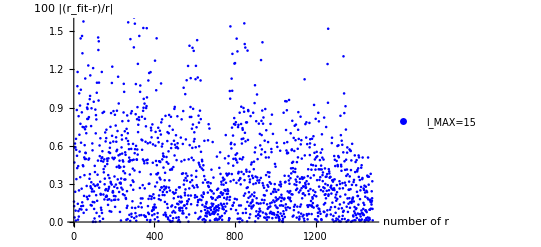

```mathematica
plotErrL15=ListPlot[Transpose[{Range[dataErrorL15//Length],dataErrorL15}],PlotStyle->Blue,AxesLabel->{Style["number\n of r",FontFamily->"Times",Medium],Style["100 |(r_fit-r)/r|",FontFamily->"Times",Medium]},PlotLegends->{Style["l_MAX=15",FontFamily->"Times"]}]
```

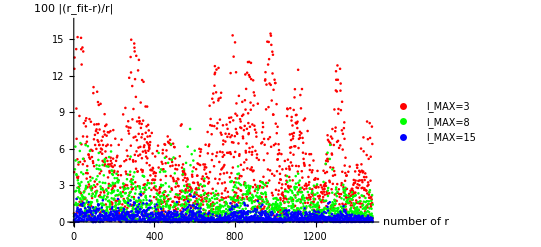

```mathematica
plotErrorsLutetia=Show[{plotErrL3,plotErrL8,plotErrL15}]
```

"ListAnimate" to show the evolution of the absolute error in the radius. “Grid” or “Row/Colomn” depending on the display.

```mathematica
Export["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/FitLutetia.eps",plotFitLutetia]
```

/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/FitLutetia.eps

```mathematica
Export["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/ErrorFitLutetia.eps",plotErrorsLutetia]
```

/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/ErrorFitLutetia.eps

Christoffel symbol in the Arfken (1985, p. 161) definition (http://mathworld.wolfram.com/ChristoffelSymboloftheSecondKind.html)

```mathematica
ChrSymblΓ={{{0,0,0},{0,-r^2 Sin[ϕ]^2,0},{0,0,-r}},{{0,1/r,0},{1/r,0,Cot[ϕ]},{0,Cot[ϕ],0}},{{0,0,1/r},{0,-Sin[ϕ]Cos[ϕ],0},{1/r,0,0}}};
```

```mathematica
ChrSymblΓ[[1]]//MatrixForm
```

(0 | 0 | 0
0 | -r^2 Sin[ϕ]^2 | 0
0 | 0 | -r)

```mathematica
ChrSymblΓ[[1]][[1,1]]
```

0

```mathematica
ChrSymblΓ[[2]]//MatrixForm
```

(0 | 1/r | 0
1/r | 0 | Cot[ϕ]
0 | Cot[ϕ] | 0)

```mathematica
ChrSymblΓ[[3]]//MatrixForm
```

(0 | 0 | 1/r
0 | -Cos[ϕ] Sin[ϕ] | 0
1/r | 0 | 0)

```mathematica
dx={xr,xθ,xϕ};
```

```mathematica
(ChrSymblΓ[[1]].dx).dx
```

-r xϕ^2-r^2 xθ^2 Sin[ϕ]^2

```mathematica
eq1= xr''[λ]-(xϕ'[λ])^2 xr[λ]-(xθ'[λ])^2 xr[λ]^2 Sin[xϕ[λ]]^2
```

-Sin[xϕ[λ]]^2 xr[λ]^2 xθ'[λ]^2-xr[λ] xϕ'[λ]^2+xr''[λ]

```mathematica
(ChrSymblΓ[[2]].dx).dx
```

(xr xθ)/r+xθ xϕ Cot[ϕ]+xθ (xr/r+xϕ Cot[ϕ])

```mathematica
eq2=xθ''[λ]+(xr'[λ] xθ'[λ])/xr[λ]+xθ'[λ] xϕ'[λ] Cot[xϕ[λ]]+xθ'[λ] (xr'[λ]/xr[λ]+xϕ'[λ] Cot[xϕ[λ]])
```

(xr'[λ] xθ'[λ])/xr[λ]+Cot[xϕ[λ]] xθ'[λ] xϕ'[λ]+xθ'[λ] (xr'[λ]/xr[λ]+Cot[xϕ[λ]] xϕ'[λ])+xθ''[λ]

```mathematica
(ChrSymblΓ[[3]].dx).dx
```

(2 xr xϕ)/r-xθ^2 Cos[ϕ] Sin[ϕ]

```mathematica
eq3=xϕ''[λ]+(2 xr'[λ] xϕ'[λ])/xr[λ]-(xθ'[λ])^2 Cos[xϕ[λ]] Sin[xϕ[λ]]
```

-Cos[xϕ[λ]] Sin[xϕ[λ]] xθ'[λ]^2+(2 xr'[λ] xϕ'[λ])/xr[λ]+xϕ''[λ]

```mathematica
DSolvepaclet:ref/DSolve[eqn,u,{x,Subscript[x, min],Subscript[x, max]}]
```

```mathematica
DSolve[{eq1==0,eq2==0,eq3==0,xr[0]==43.4595217689482,xθ[0]==0.9694357065710962,xϕ[0]==2.2808477591782625,xr'[0]==1,xθ'[0]==1,xϕ'[0]==1},{xr[λ],xθ[λ],xϕ[λ]},{λ}]
```

DSolve[{-Sin[xϕ[λ]]^2 xr[λ]^2 xθ'[λ]^2-xr[λ] xϕ'[λ]^2+xr''[λ]==0,(xr'[λ] xθ'[λ])/xr[λ]+Cot[xϕ[λ]] xθ'[λ] xϕ'[λ]+xθ'[λ] (xr'[λ]/xr[λ]+Cot[xϕ[λ]] xϕ'[λ])+xθ''[λ]==0,-Cos[xϕ[λ]] Sin[xϕ[λ]] xθ'[λ]^2+(2 xr'[λ] xϕ'[λ])/xr[λ]+xϕ''[λ]==0,xr[0]==43.4595,xθ[0]==0.969436,xϕ[0]==2.28085,xr'[0]==1,xθ'[0]==1,xϕ'[0]==1},{xr[λ],xθ[λ],xϕ[λ]},{λ}]

```mathematica
{0.9694357065710962,2.2808477591782625,43.4595217689482}
```

```mathematica
sol=NDSolve[{eq1==0,eq2==0,eq3==0,xr[0]==43.4595217689482,xθ[0]==0.9694357065710962,xϕ[0]==2.2808477591782625,xr'[0]==1,xθ'[0]==1,xϕ'[0]==1},{xr[λ],xθ[λ],xϕ[λ]},{λ,0,1}]
```

{{xr[λ]→InterpolatingFunction[…][λ],xθ[λ]→InterpolatingFunction[…][λ],xϕ[λ]→InterpolatingFunction[…][λ]}}

```mathematica
Plot[{(*xr[λ]/.sol[[1]],*)xθ[λ]/.sol[[2]](*,xϕ[λ]/.sol[[3]]*)},{λ,0,1},PlotRange->All]
```

Part::partw: Part 2 of {{xr[0.0000204286]→43.4595,xθ[0.0000204286]→0.969456,xϕ[0.0000204286]→2.28087}} does not exist.

ReplaceAll::reps: {{{xr[0.0000204286]→43.4595,xθ[0.0000204286]→0.969456,xϕ[0.0000204286]→2.28087}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{xr[0.0204286]→43.7178,xθ[0.0204286]→0.990145,xϕ[0.0204286]→2.30109}} does not exist.

ReplaceAll::reps: {{{xr[0.0204286]→43.7178,xθ[0.0204286]→0.990145,xϕ[0.0204286]→2.30109}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{xr[0.0408368]→44.4557,xθ[0.0408368]→1.0111,xϕ[0.0408368]→2.32064}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{xr[0.0408368]→44.4557,xθ[0.0408368]→1.0111,xϕ[0.0408368]→2.32064}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

# Calculating the Christoffel symbol

```mathematica
ClearAll
```

ClearAll

```mathematica
op[t_]=D[#,t]+2#&
```

∂_t #1+2 #1&

```mathematica
op[θ][Sin[θ]]
```

Cos[θ]+2 Sin[θ]

```mathematica
pder[u_,v_]=D[#,u]+D[#,{v,2}]&
```

∂_u #1+∂_{v,2} #1&

```mathematica
pder[x,y][Sin[x]+x y^2]
```

2 x+y^2+Cos[x]

```mathematica
pder2[u_,v_]:={D[#,u],D[#,v]}&
```

```mathematica
pder2[x,y][Sin[x y]+y^2]
```

{y Cos[x y],2 y+x Cos[x y]}

```mathematica
pder2[y][Cos[y]+x^2]
```

-Sin[y]

```mathematica
{pder[x][Sin[x]+a],pder[a][Sin[x]+a]}
```

{Cos[x],1}

```mathematica
g={{r^2+(Subscript[pdr, θ])^2,(Subscript[pdr, θ])(Subscript[pdr, ϕ])},{Subscript[pdr, θ] Subscript[pdr, ϕ],r^2 Sin[θ]^2+(Subscript[pdr, ϕ])^2}}
```

{{r^2+pdr_θ^2,pdr_θ pdr_ϕ},{pdr_θ pdr_ϕ,r^2 Sin[θ]^2+pdr_ϕ^2}}

```mathematica
g//MatrixForm
```

(r^2+pdr_θ^2 | pdr_θ pdr_ϕ
pdr_θ pdr_ϕ | r^2 Sin[θ]^2+pdr_ϕ^2)

```mathematica
Det[g]
```

r^4 Sin[θ]^2+r^2 Sin[θ]^2 pdr_θ^2+r^2 pdr_ϕ^2

```mathematica
Inverse[g]//Simplify
```

{{(r^2 Sin[θ]^2+pdr_ϕ^2)/(r^2 (r^2 Sin[θ]^2+Sin[θ]^2 pdr_θ^2+pdr_ϕ^2)),-(pdr_θ pdr_ϕ)/(r^2 (r^2 Sin[θ]^2+Sin[θ]^2 pdr_θ^2+pdr_ϕ^2))},{-(pdr_θ pdr_ϕ)/(r^2 (r^2 Sin[θ]^2+Sin[θ]^2 pdr_θ^2+pdr_ϕ^2)),(r^2+pdr_θ^2)/(r^2 (r^2 Sin[θ]^2+Sin[θ]^2 pdr_θ^2+pdr_ϕ^2))}}

```mathematica
gInv=1/(r^2 Sin[θ]^2+Sin[θ]^2 Subscript[pdr, θ]^2+Subscript[pdr, ϕ]^2){{Sin[θ]^2+Subscript[pdr, ϕ]^2/r^2,-(Subscript[pdr, θ] Subscript[pdr, ϕ])/r^2},{-(Subscript[pdr, θ] Subscript[pdr, ϕ])/r^2,1+Subscript[pdr, θ]^2/r^2}};
```

```mathematica
g.gInv//Simplify//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
{{Sin[θ]^2+Subscript[pdr, ϕ]^2/r^2,-(Subscript[pdr, θ] Subscript[pdr, ϕ])/r^2},{-(Subscript[pdr, θ] Subscript[pdr, ϕ])/r^2,1+Subscript[pdr, θ]^2/r^2}}//MatrixForm
```

(Sin[θ]^2+pdr_ϕ^2/r^2 | -(pdr_θ pdr_ϕ)/r^2
-(pdr_θ pdr_ϕ)/r^2 | 1+pdr_θ^2/r^2)

```mathematica
Og[θ_,ϕ_]={{#^2+D[#,θ]^2,D[#,θ]D[#,ϕ]},{D[#,θ]D[#,ϕ],#^2 Sin[θ]^2+D[#,ϕ]^2}}&
```

{{#1^2+(∂_θ #1)^2,∂_θ #1 ∂_ϕ #1},{∂_θ #1 ∂_ϕ #1,#1^2 Sin[θ]^2+(∂_ϕ #1)^2}}&

```mathematica
OgInv[θ_,ϕ_]=1/(#^2 Sin[θ]^2+Sin[θ]^2 D[#,θ]^2+D[#,ϕ]^2){{Sin[θ]^2+D[#,ϕ]^2/#^2,-(D[#,θ] D[#,ϕ])/#^2},{-(D[#,θ] D[#,ϕ])/#^2,1+D[#,θ]^2/#^2}}&
```

{{Sin[θ]^2+(∂_ϕ #1)^2/#1^2,-(∂_θ #1 ∂_ϕ #1)/#1^2},{-(∂_θ #1 ∂_ϕ #1)/#1^2,1+(∂_θ #1)^2/#1^2}}/(#1^2 Sin[θ]^2+Sin[θ]^2 (∂_θ #1)^2+(∂_ϕ #1)^2)&

## Calculating the first component Γ_(β μ)^θ

```mathematica
rFitLutetia[θ,ϕ]
```

54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]

```mathematica
(*FullSimplify[Og[θ,ϕ][rFitLutetia[θ,ϕ]],{θ≥0,θ≤π,ϕ>-π,ϕ≤π}]*)
```

$Aborted

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},Og[θ,ϕ][rFitLutetia[θ,ϕ]]//Simplify]
```

{{(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2,(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))},{(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))),(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2}}

```mathematica
gFit[θ_,ϕ_]:={{(54.348611211485164-1.4425591445501287 Cos[4 ϕ]-2.209429381828982 Cos[ϕ] Sin[θ]+2.818318784549385 Cos[3 ϕ] Sin[θ]^3+0.5926815015846589 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.5485234942542312-1.450342390847195 Sin[θ]^2)+10.792514116115738 Cos[ϕ] Sin[ϕ]+0.310776231872863 Sin[θ] Sin[ϕ]+0.34963231611902584 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.09501125348435324 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.816394486903914-1.4425591445501287 Cos[4 ϕ]-9.87471576073588 Cos[ϕ] Sin[θ]+8.262904985870692 Sin[θ] Sin[ϕ]-0.7105735562332913 Sin[4 ϕ])+Cos[θ]^5 (8.162834015917953-1.8501410274585612 Cos[4 ϕ]-0.6536043000716671 Sin[4 ϕ])+Cos[θ] (-0.8294685911214945-1.8501410274585612 Cos[4 ϕ]-0.6949134283251226 Cos[ϕ] Sin[θ]-3.4232932422692173 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.2553780488396649-2.552641824321018 Sin[θ]^2)-0.04496785438214449 Cos[ϕ] Sin[ϕ]+5.076578690838504 Sin[θ] Sin[ϕ]-0.44401242319781603 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8363977427433156 Sin[θ]^3 Sin[3 ϕ]-0.6536043000716671 Sin[4 ϕ])-0.7105735562332913 Sin[4 ϕ]+Cos[θ]^3 (-3.829203361665252+3.7002820549171225 Cos[4 ϕ]+5.701583504162247 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.2553780488396649+7.657925472963054 Sin[θ]^2)+0.04496785438214449 Cos[ϕ] Sin[ϕ]-13.26738416110994 Sin[θ] Sin[ϕ]+1.3320372695934481 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.3072086001433343 Sin[4 ϕ])+Cos[θ]^2 (-20.84443005322268+2.8851182891002574 Cos[4 ϕ]+17.870930309173815 Cos[ϕ] Sin[θ]+0.7477290031628104 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.5485234942542312+10.152396735930365 Sin[θ]^2)-10.792514116115738 Cos[ϕ] Sin[ϕ]-2.1813831855957346 Sin[θ] Sin[ϕ]-2.447426212833181 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.946030327967996 Sin[θ]^3 Sin[3 ϕ]+1.4211471124665827 Sin[4 ϕ])+1.1725246339950335 Sin[θ]^5 Sin[5 ϕ])^2+(Cos[θ]^5 (-9.87471576073588 Cos[ϕ]+8.262904985870692 Sin[ϕ])+Cos[θ]^2 (-22.973776418889162 Cos[2 ϕ] Sin[θ]^3+5.076578690838504 Sin[ϕ]+Cos[ϕ] (-0.6949134283251226-17.104750512486742 Sin[θ]^2-1.0229284095420654 Sin[θ] Sin[ϕ]-3.9961118087803444 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.269879726807652 Cos[3 ϕ]+39.80215248332982 Sin[ϕ]-11.509193228229947 Sin[3 ϕ])+Sin[θ] (11.487610084995756-1.3391495021230417 Cos[2 ϕ]-11.100846164751367 Cos[4 ϕ]-3.921625800430003 Sin[4 ϕ]))+Sin[θ] (0.8294685911214945+1.8501410274585612 Cos[4 ϕ]+0.6949134283251226 Cos[ϕ] Sin[θ]+3.4232932422692173 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.2553780488396649+2.552641824321018 Sin[θ]^2)+0.04496785438214449 Cos[ϕ] Sin[ϕ]-5.076578690838504 Sin[θ] Sin[ϕ]+0.44401242319781603 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8363977427433156 Sin[θ]^3 Sin[3 ϕ]+0.6536043000716671 Sin[4 ϕ])+Cos[θ]^3 (-2.1813831855957346 Sin[ϕ]+Cos[ϕ] (17.870930309173815+39.49886304294352 Sin[θ]^2-4.894852425666362 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.243187009488431 Cos[3 ϕ]-33.05161994348277 Sin[ϕ]+20.83809098390399 Sin[3 ϕ])+Sin[θ] (-19.265577947615657+20.30479347186073 Cos[2 ϕ]+5.770236578200515 Cos[4 ϕ]+2.8422942249331653 Sin[4 ϕ]))+Cos[θ]^4 (-13.26738416110994 Sin[ϕ]+Cos[ϕ] (5.701583504162247+2.6640745391868963 Sin[θ] Sin[ϕ])+Sin[θ] (-40.81417007958977+15.315850945926108 Cos[2 ϕ]+9.250705137292806 Cos[4 ϕ]+3.2680215003583357 Sin[4 ϕ]))+Cos[θ] (-20.30479347186073 Cos[2 ϕ] Sin[θ]^3+0.310776231872863 Sin[ϕ]+Cos[ϕ] (-2.209429381828982-35.74186061834763 Sin[θ]^2+22.284292864469528 Sin[θ] Sin[ϕ]+4.894852425666362 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.454956353648155 Cos[3 ϕ]+4.362766371191469 Sin[ϕ]+0.2850337604530597 Sin[3 ϕ])+Sin[θ] (41.68886010644536-3.9977317702028525 Cos[2 ϕ]-5.770236578200515 Cos[4 ϕ]-2.8422942249331653 Sin[4 ϕ])+Sin[θ]^4 (-1.4954580063256209 Cos[3 ϕ]+2.9634075079232947 Cos[5 ϕ]-13.892060655935992 Sin[3 ϕ]+5.862623169975167 Sin[5 ϕ])))^2,(10.792514116115738 Cos[ϕ]^2-2.8422942249331653 Cos[4 ϕ]+0.310776231872863 Cos[ϕ] Sin[θ]+0.34963231611902584 Cos[ϕ]^2 Sin[θ]^2+0.2850337604530597 Cos[3 ϕ] Sin[θ]^3+5.862623169975167 Cos[5 ϕ] Sin[θ]^5+2.209429381828982 Sin[θ] Sin[ϕ]-10.792514116115738 Sin[ϕ]^2-0.34963231611902584 Sin[θ]^2 Sin[ϕ]^2+2.90068478169439 (0.3782027593731296+1. Sin[θ]^2) Sin[2 ϕ]-8.454956353648155 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.228834400573337 Cos[4 ϕ]+Cos[ϕ]^2 (0.04496785438214449+1.3320372695934481 Sin[θ]^2)-5.701583504162247 Sin[θ] Sin[ϕ]-0.04496785438214449 Sin[ϕ]^2-1.3320372695934481 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.26738416110994 Sin[θ]+5.0215121953586594 Sin[ϕ]-30.631701891852217 Sin[θ]^2 Sin[ϕ])-14.80112821966849 Sin[4 ϕ])+Cos[θ]^2 (5.684588449866331 Cos[4 ϕ]+20.83809098390399 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.792514116115738-2.447426212833181 Sin[θ]^2)-17.870930309173815 Sin[θ] Sin[ϕ]+10.792514116115738 Sin[ϕ]^2+2.447426212833181 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.1813831855957346 Sin[θ]-2.1940939770169248 Sin[ϕ]-40.60958694372146 Sin[θ]^2 Sin[ϕ])-2.243187009488431 Sin[θ]^3 Sin[3 ϕ]-11.54047315640103 Sin[4 ϕ])+5.770236578200515 Sin[4 ϕ]+Cos[θ]^4 (-2.8422942249331653 Cos[4 ϕ]+8.262904985870692 Cos[ϕ] Sin[θ]+9.87471576073588 Sin[θ] Sin[ϕ]+5.770236578200515 Sin[4 ϕ])+Cos[θ]^5 (-2.6144172002866686 Cos[4 ϕ]+7.400564109834245 Sin[4 ϕ])+Cos[θ] (-2.6144172002866686 Cos[4 ϕ]-11.509193228229947 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.04496785438214449-0.44401242319781603 Sin[θ]^2)+0.6949134283251226 Sin[θ] Sin[ϕ]+0.04496785438214449 Sin[ϕ]^2+0.44401242319781603 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.076578690838504 Sin[θ]-5.0215121953586594 Sin[ϕ]+10.210567297284072 Sin[θ]^2 Sin[ϕ])+10.269879726807652 Sin[θ]^3 Sin[3 ϕ]+7.400564109834245 Sin[4 ϕ])-2.9634075079232947 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87471576073588 Cos[ϕ]+8.262904985870692 Sin[ϕ])+Cos[θ]^2 (-22.973776418889162 Cos[2 ϕ] Sin[θ]^3+5.076578690838504 Sin[ϕ]+Cos[ϕ] (-0.6949134283251226-17.104750512486742 Sin[θ]^2-1.0229284095420654 Sin[θ] Sin[ϕ]-3.9961118087803444 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.269879726807652 Cos[3 ϕ]+39.80215248332982 Sin[ϕ]-11.509193228229947 Sin[3 ϕ])+Sin[θ] (11.487610084995756-1.3391495021230417 Cos[2 ϕ]-11.100846164751367 Cos[4 ϕ]-3.921625800430003 Sin[4 ϕ]))+Sin[θ] (0.8294685911214945+1.8501410274585612 Cos[4 ϕ]+0.6949134283251226 Cos[ϕ] Sin[θ]+3.4232932422692173 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.2553780488396649+2.552641824321018 Sin[θ]^2)+0.04496785438214449 Cos[ϕ] Sin[ϕ]-5.076578690838504 Sin[θ] Sin[ϕ]+0.44401242319781603 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8363977427433156 Sin[θ]^3 Sin[3 ϕ]+0.6536043000716671 Sin[4 ϕ])+Cos[θ]^3 (-2.1813831855957346 Sin[ϕ]+Cos[ϕ] (17.870930309173815+39.49886304294352 Sin[θ]^2-4.894852425666362 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.243187009488431 Cos[3 ϕ]-33.05161994348277 Sin[ϕ]+20.83809098390399 Sin[3 ϕ])+Sin[θ] (-19.265577947615657+20.30479347186073 Cos[2 ϕ]+5.770236578200515 Cos[4 ϕ]+2.8422942249331653 Sin[4 ϕ]))+Cos[θ]^4 (-13.26738416110994 Sin[ϕ]+Cos[ϕ] (5.701583504162247+2.6640745391868963 Sin[θ] Sin[ϕ])+Sin[θ] (-40.81417007958977+15.315850945926108 Cos[2 ϕ]+9.250705137292806 Cos[4 ϕ]+3.2680215003583357 Sin[4 ϕ]))+Cos[θ] (-20.30479347186073 Cos[2 ϕ] Sin[θ]^3+0.310776231872863 Sin[ϕ]+Cos[ϕ] (-2.209429381828982-35.74186061834763 Sin[θ]^2+22.284292864469528 Sin[θ] Sin[ϕ]+4.894852425666362 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.454956353648155 Cos[3 ϕ]+4.362766371191469 Sin[ϕ]+0.2850337604530597 Sin[3 ϕ])+Sin[θ] (41.68886010644536-3.9977317702028525 Cos[2 ϕ]-5.770236578200515 Cos[4 ϕ]-2.8422942249331653 Sin[4 ϕ])+Sin[θ]^4 (-1.4954580063256209 Cos[3 ϕ]+2.9634075079232947 Cos[5 ϕ]-13.892060655935992 Sin[3 ϕ]+5.862623169975167 Sin[5 ϕ])))},{(10.792514116115738 Cos[ϕ]^2-2.8422942249331653 Cos[4 ϕ]+0.310776231872863 Cos[ϕ] Sin[θ]+0.34963231611902584 Cos[ϕ]^2 Sin[θ]^2+0.2850337604530597 Cos[3 ϕ] Sin[θ]^3+5.862623169975167 Cos[5 ϕ] Sin[θ]^5+2.209429381828982 Sin[θ] Sin[ϕ]-10.792514116115738 Sin[ϕ]^2-0.34963231611902584 Sin[θ]^2 Sin[ϕ]^2+2.90068478169439 (0.3782027593731296+1. Sin[θ]^2) Sin[2 ϕ]-8.454956353648155 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.228834400573337 Cos[4 ϕ]+Cos[ϕ]^2 (0.04496785438214449+1.3320372695934481 Sin[θ]^2)-5.701583504162247 Sin[θ] Sin[ϕ]-0.04496785438214449 Sin[ϕ]^2-1.3320372695934481 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.26738416110994 Sin[θ]+5.0215121953586594 Sin[ϕ]-30.631701891852217 Sin[θ]^2 Sin[ϕ])-14.80112821966849 Sin[4 ϕ])+Cos[θ]^2 (5.684588449866331 Cos[4 ϕ]+20.83809098390399 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.792514116115738-2.447426212833181 Sin[θ]^2)-17.870930309173815 Sin[θ] Sin[ϕ]+10.792514116115738 Sin[ϕ]^2+2.447426212833181 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.1813831855957346 Sin[θ]-2.1940939770169248 Sin[ϕ]-40.60958694372146 Sin[θ]^2 Sin[ϕ])-2.243187009488431 Sin[θ]^3 Sin[3 ϕ]-11.54047315640103 Sin[4 ϕ])+5.770236578200515 Sin[4 ϕ]+Cos[θ]^4 (-2.8422942249331653 Cos[4 ϕ]+8.262904985870692 Cos[ϕ] Sin[θ]+9.87471576073588 Sin[θ] Sin[ϕ]+5.770236578200515 Sin[4 ϕ])+Cos[θ]^5 (-2.6144172002866686 Cos[4 ϕ]+7.400564109834245 Sin[4 ϕ])+Cos[θ] (-2.6144172002866686 Cos[4 ϕ]-11.509193228229947 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.04496785438214449-0.44401242319781603 Sin[θ]^2)+0.6949134283251226 Sin[θ] Sin[ϕ]+0.04496785438214449 Sin[ϕ]^2+0.44401242319781603 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.076578690838504 Sin[θ]-5.0215121953586594 Sin[ϕ]+10.210567297284072 Sin[θ]^2 Sin[ϕ])+10.269879726807652 Sin[θ]^3 Sin[3 ϕ]+7.400564109834245 Sin[4 ϕ])-2.9634075079232947 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87471576073588 Cos[ϕ]+8.262904985870692 Sin[ϕ])+Cos[θ]^2 (-22.973776418889162 Cos[2 ϕ] Sin[θ]^3+5.076578690838504 Sin[ϕ]+Cos[ϕ] (-0.6949134283251226-17.104750512486742 Sin[θ]^2-1.0229284095420654 Sin[θ] Sin[ϕ]-3.9961118087803444 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.269879726807652 Cos[3 ϕ]+39.80215248332982 Sin[ϕ]-11.509193228229947 Sin[3 ϕ])+Sin[θ] (11.487610084995756-1.3391495021230417 Cos[2 ϕ]-11.100846164751367 Cos[4 ϕ]-3.921625800430003 Sin[4 ϕ]))+Sin[θ] (0.8294685911214945+1.8501410274585612 Cos[4 ϕ]+0.6949134283251226 Cos[ϕ] Sin[θ]+3.4232932422692173 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.2553780488396649+2.552641824321018 Sin[θ]^2)+0.04496785438214449 Cos[ϕ] Sin[ϕ]-5.076578690838504 Sin[θ] Sin[ϕ]+0.44401242319781603 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8363977427433156 Sin[θ]^3 Sin[3 ϕ]+0.6536043000716671 Sin[4 ϕ])+Cos[θ]^3 (-2.1813831855957346 Sin[ϕ]+Cos[ϕ] (17.870930309173815+39.49886304294352 Sin[θ]^2-4.894852425666362 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.243187009488431 Cos[3 ϕ]-33.05161994348277 Sin[ϕ]+20.83809098390399 Sin[3 ϕ])+Sin[θ] (-19.265577947615657+20.30479347186073 Cos[2 ϕ]+5.770236578200515 Cos[4 ϕ]+2.8422942249331653 Sin[4 ϕ]))+Cos[θ]^4 (-13.26738416110994 Sin[ϕ]+Cos[ϕ] (5.701583504162247+2.6640745391868963 Sin[θ] Sin[ϕ])+Sin[θ] (-40.81417007958977+15.315850945926108 Cos[2 ϕ]+9.250705137292806 Cos[4 ϕ]+3.2680215003583357 Sin[4 ϕ]))+Cos[θ] (-20.30479347186073 Cos[2 ϕ] Sin[θ]^3+0.310776231872863 Sin[ϕ]+Cos[ϕ] (-2.209429381828982-35.74186061834763 Sin[θ]^2+22.284292864469528 Sin[θ] Sin[ϕ]+4.894852425666362 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.454956353648155 Cos[3 ϕ]+4.362766371191469 Sin[ϕ]+0.2850337604530597 Sin[3 ϕ])+Sin[θ] (41.68886010644536-3.9977317702028525 Cos[2 ϕ]-5.770236578200515 Cos[4 ϕ]-2.8422942249331653 Sin[4 ϕ])+Sin[θ]^4 (-1.4954580063256209 Cos[3 ϕ]+2.9634075079232947 Cos[5 ϕ]-13.892060655935992 Sin[3 ϕ]+5.862623169975167 Sin[5 ϕ]))),(10.792514116115738 Cos[ϕ]^2-2.8422942249331653 Cos[4 ϕ]+0.310776231872863 Cos[ϕ] Sin[θ]+0.34963231611902584 Cos[ϕ]^2 Sin[θ]^2+0.2850337604530597 Cos[3 ϕ] Sin[θ]^3+5.862623169975167 Cos[5 ϕ] Sin[θ]^5+2.209429381828982 Sin[θ] Sin[ϕ]-10.792514116115738 Sin[ϕ]^2-0.34963231611902584 Sin[θ]^2 Sin[ϕ]^2+2.90068478169439 (0.3782027593731296+1. Sin[θ]^2) Sin[2 ϕ]-8.454956353648155 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.228834400573337 Cos[4 ϕ]+Cos[ϕ]^2 (0.04496785438214449+1.3320372695934481 Sin[θ]^2)-5.701583504162247 Sin[θ] Sin[ϕ]-0.04496785438214449 Sin[ϕ]^2-1.3320372695934481 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.26738416110994 Sin[θ]+5.0215121953586594 Sin[ϕ]-30.631701891852217 Sin[θ]^2 Sin[ϕ])-14.80112821966849 Sin[4 ϕ])+Cos[θ]^2 (5.684588449866331 Cos[4 ϕ]+20.83809098390399 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.792514116115738-2.447426212833181 Sin[θ]^2)-17.870930309173815 Sin[θ] Sin[ϕ]+10.792514116115738 Sin[ϕ]^2+2.447426212833181 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.1813831855957346 Sin[θ]-2.1940939770169248 Sin[ϕ]-40.60958694372146 Sin[θ]^2 Sin[ϕ])-2.243187009488431 Sin[θ]^3 Sin[3 ϕ]-11.54047315640103 Sin[4 ϕ])+5.770236578200515 Sin[4 ϕ]+Cos[θ]^4 (-2.8422942249331653 Cos[4 ϕ]+8.262904985870692 Cos[ϕ] Sin[θ]+9.87471576073588 Sin[θ] Sin[ϕ]+5.770236578200515 Sin[4 ϕ])+Cos[θ]^5 (-2.6144172002866686 Cos[4 ϕ]+7.400564109834245 Sin[4 ϕ])+Cos[θ] (-2.6144172002866686 Cos[4 ϕ]-11.509193228229947 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.04496785438214449-0.44401242319781603 Sin[θ]^2)+0.6949134283251226 Sin[θ] Sin[ϕ]+0.04496785438214449 Sin[ϕ]^2+0.44401242319781603 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.076578690838504 Sin[θ]-5.0215121953586594 Sin[ϕ]+10.210567297284072 Sin[θ]^2 Sin[ϕ])+10.269879726807652 Sin[θ]^3 Sin[3 ϕ]+7.400564109834245 Sin[4 ϕ])-2.9634075079232947 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.348611211485164-1.4425591445501287 Cos[4 ϕ]-2.209429381828982 Cos[ϕ] Sin[θ]+2.818318784549385 Cos[3 ϕ] Sin[θ]^3+0.5926815015846589 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.5485234942542312-1.450342390847195 Sin[θ]^2)+10.792514116115738 Cos[ϕ] Sin[ϕ]+0.310776231872863 Sin[θ] Sin[ϕ]+0.34963231611902584 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.09501125348435324 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.816394486903914-1.4425591445501287 Cos[4 ϕ]-9.87471576073588 Cos[ϕ] Sin[θ]+8.262904985870692 Sin[θ] Sin[ϕ]-0.7105735562332913 Sin[4 ϕ])+Cos[θ]^5 (8.162834015917953-1.8501410274585612 Cos[4 ϕ]-0.6536043000716671 Sin[4 ϕ])+Cos[θ] (-0.8294685911214945-1.8501410274585612 Cos[4 ϕ]-0.6949134283251226 Cos[ϕ] Sin[θ]-3.4232932422692173 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.2553780488396649-2.552641824321018 Sin[θ]^2)-0.04496785438214449 Cos[ϕ] Sin[ϕ]+5.076578690838504 Sin[θ] Sin[ϕ]-0.44401242319781603 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8363977427433156 Sin[θ]^3 Sin[3 ϕ]-0.6536043000716671 Sin[4 ϕ])-0.7105735562332913 Sin[4 ϕ]+Cos[θ]^3 (-3.829203361665252+3.7002820549171225 Cos[4 ϕ]+5.701583504162247 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.2553780488396649+7.657925472963054 Sin[θ]^2)+0.04496785438214449 Cos[ϕ] Sin[ϕ]-13.26738416110994 Sin[θ] Sin[ϕ]+1.3320372695934481 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.3072086001433343 Sin[4 ϕ])+Cos[θ]^2 (-20.84443005322268+2.8851182891002574 Cos[4 ϕ]+17.870930309173815 Cos[ϕ] Sin[θ]+0.7477290031628104 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.5485234942542312+10.152396735930365 Sin[θ]^2)-10.792514116115738 Cos[ϕ] Sin[ϕ]-2.1813831855957346 Sin[θ] Sin[ϕ]-2.447426212833181 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.946030327967996 Sin[θ]^3 Sin[3 ϕ]+1.4211471124665827 Sin[4 ϕ])+1.1725246339950335 Sin[θ]^5 Sin[5 ϕ])^2}}
```

```mathematica
(*FullSimplify[OgInv[θ,ϕ][rFitLutetia[θ,ϕ]],{θ≥0,θ≤π,ϕ>-π,ϕ≤π}]*)
```

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},OgInv[θ,ϕ][rFitLutetia[θ,ϕ]]//Simplify]
```

{{(Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2),-(((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))},{-(((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))),(1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2)/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)}}

```mathematica
gInvFit[θ_,ϕ_]:=
```

```mathematica
With[{θ=π/12,ϕ=-π/3},gFit[θ,ϕ].gInvFit[θ,ϕ]//MatrixForm]
```

(1. | 0.
0. | 1.)

```mathematica
(*({{r^2+Subscript[pdr, θ]^2, Subscript[pdr, θ] Subscript[pdr, ϕ]}, {Subscript[pdr, θ] Subscript[pdr, ϕ], r^2 Sin[θ]^2+Subscript[pdr, ϕ]^2}})
1/(r^2 Sin[θ]^2+Sin[θ]^2 Subscript[pdr, θ]^2+Subscript[pdr, ϕ]^2){{Sin[θ]^2+Subscript[pdr, ϕ]^2/r^2,-(Subscript[pdr, θ] Subscript[pdr, ϕ])/r^2},{-(Subscript[pdr, θ] Subscript[pdr, ϕ])/r^2,1+Subscript[pdr, θ]^2/r^2}};*)
```

```mathematica
(*Opdgθ[θ_,ϕ_]={{2# D[#,θ]+2D[#,θ]D[#,{θ,2}],D[#,{θ,2}] D[#,ϕ]+D[#,θ]D[#,{ϕ,1},{θ,1}]},{D[#,{θ,2}] D[#,ϕ]+D[#,θ]D[#,{ϕ,1},{θ,1}],2# D[#,θ] Sin[θ]^2+2#^2 Sin[θ]Cos[θ]+2D[#,ϕ]D[#,{ϕ,1},{θ,1}]}}&*)
```

```mathematica
(*Opdgϕ[θ_,ϕ_]={{2# D[#,ϕ]+2D[#,θ]D[#,{θ,1},{ϕ,1}], D[#,{θ,1},{ϕ,1}]D[#,ϕ]+D[#,θ]D[#,{ϕ,2}]},{D[#,{θ,1},{ϕ,1}]D[#,ϕ]+D[#,θ]D[#,{ϕ,2}],2# D[#,ϕ] Sin[θ]^2+2D[#,ϕ]D[#,{ϕ,2}]}}&*)
```

```mathematica
(*1/2 OgInv[θ,ϕ][f[θ,ϕ]]//Simplify*)
```

```mathematica
(*FullSimplify[D[gFit[θ,ϕ],θ],{θ≥0,θ≤π,ϕ>-π,ϕ≤π}]*)
```

{{-15.5394 Sin[θ]+Cos[θ] (-14.7271 Cos[ϕ]-24.5298 Sin[ϕ]),0.0360285 (1. Cos[ϕ]-0.600374 Sin[ϕ]) (2.11032 Cos[θ] Sin[θ]+Sin[θ]^2 (-1. Cos[ϕ]-1.66563 Sin[ϕ])+Cos[θ]^2 (1. Cos[ϕ]+1.66563 Sin[ϕ]))},{0.0360285 (1. Cos[ϕ]-0.600374 Sin[ϕ]) (2.11032 Cos[θ] Sin[θ]+Sin[θ]^2 (-1. Cos[ϕ]-1.66563 Sin[ϕ])+Cos[θ]^2 (1. Cos[ϕ]+1.66563 Sin[ϕ])),2 Sin[θ] (Cos[θ] (0.24497 Cos[ϕ]-0.147073 Sin[ϕ])^2+Sin[θ] (-0.155186 Sin[θ]+Cos[θ] (-0.147073 Cos[ϕ]-0.24497 Sin[ϕ])) (50.0671+0.155186 Cos[θ]-0.147073 Cos[ϕ] Sin[θ]-0.24497 Sin[θ] Sin[ϕ])+Cos[θ] (50.0671+0.155186 Cos[θ]-0.147073 Cos[ϕ] Sin[θ]-0.24497 Sin[θ] Sin[ϕ])^2)}}

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},D[gFit[θ,ϕ],θ]//Simplify]
```

{{2 (54.3486-1.44256 Cos[4 ϕ]-41.6889 Sin[θ]^2+5.77024 Cos[4 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-5.63664 Cos[3 ϕ] Sin[θ]^3+1.49546 Cos[3 ϕ] Sin[θ]^5-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523+2.54739 Sin[θ]^2+20.3048 Sin[θ]^4)+14.4492 Sin[2 θ]^2+10.7925 Cos[ϕ] Sin[ϕ]-21.9347 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+3.36521 Sin[2 θ]^2 Sin[2 ϕ]-0.190023 Sin[θ]^3 Sin[3 ϕ]+13.8921 Sin[θ]^5 Sin[3 ϕ]-0.710574 Sin[4 ϕ]+2.84229 Sin[θ]^2 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^4 (-14.4492+20.3048 Cos[2 ϕ]+4.32768 Cos[4 ϕ]+118.497 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-99.1549 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.13172 Sin[4 ϕ])+Cos[θ]^5 (-32.6513+15.3159 Cos[2 ϕ]+7.40056 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+2.61442 Sin[4 ϕ])+Cos[θ]^3 (7.65841-51.3143 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-2.59453-122.527 Sin[θ]^2)+Cos[4 ϕ] (-7.40056-37.0028 Sin[θ]^2)-0.977961 Cos[ϕ] Sin[ϕ]+119.406 Sin[θ] Sin[ϕ]-21.3126 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-2.61442 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] Sin[θ] (45.9476 Cos[2 ϕ] Sin[θ]^3-15.2297 Sin[ϕ]+Cos[ϕ] (2.08474+34.2095 Sin[θ]^2+2.93388 Sin[θ] Sin[ϕ]+7.99222 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (30.8096 Cos[3 ϕ]-79.6043 Sin[ϕ]+34.5276 Sin[3 ϕ])+Sin[θ] (-22.9752+7.78358 Cos[2 ϕ]+22.2017 Cos[4 ϕ]+7.84325 Sin[4 ϕ]))-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (20.8444-107.226 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]-118.497 Cos[ϕ] Sin[θ]^3-11.9637 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.44921-111.676 Sin[θ]^2)+Cos[4 ϕ] (-2.88512-17.3107 Sin[θ]^2)+11.4918 Cos[ϕ] Sin[ϕ]+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-111.136 Sin[θ]^3 Sin[3 ϕ]-1.42115 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))),(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))},{(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))),2 (Cos[θ] Sin[θ] (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ]))+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))))}}

```mathematica
dgFitθ[θ_,ϕ_]:=
```

```mathematica
(*FullSimplify[D[gFit[θ,ϕ],ϕ],{θ≥0,θ≤π,ϕ>-π,ϕ≤π}]*)
```

{{0.0720569 Cos[ϕ]^2+Cos[ϕ] (-24.5298 Sin[θ]+0.0767591 Sin[ϕ])+(14.7271 Sin[θ]-0.0720569 Sin[ϕ]) Sin[ϕ],Sin[θ] (Sin[θ] (-0.0228237 Cos[ϕ]-0.0380158 Sin[ϕ])+Cos[θ] (0.0383795 Cos[2 ϕ]-0.144114 Cos[ϕ] Sin[ϕ]))},{Sin[θ] (Sin[θ] (-0.0228237 Cos[ϕ]-0.0380158 Sin[ϕ])+Cos[θ] (0.0383795 Cos[2 ϕ]-0.144114 Cos[ϕ] Sin[ϕ])),2 Sin[θ]^2 (-0.0360285 Cos[ϕ]^2-0.0383795 Cos[ϕ] Sin[ϕ]+0.0360285 Sin[ϕ]^2+Sin[θ] (-0.24497 Cos[ϕ]+0.147073 Sin[ϕ]) (50.0671+0.155186 Cos[θ]-0.147073 Cos[ϕ] Sin[θ]-0.24497 Sin[θ] Sin[ϕ]))}}

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},D[gFit[θ,ϕ],ϕ]//Simplify]
```

{{2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))),(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))},{(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))),2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]))}}

```mathematica
dgFitϕ[θ_,ϕ_]:=
```

```mathematica
(*gFit[θ,ϕ],gInvFit[θ,ϕ],dgFitθ[θ,ϕ],dgFitϕ[θ,ϕ]*)
{{θθ,θϕ},{ϕθ,ϕϕ}}//MatrixForm
```

(θθ | θϕ
ϕθ | ϕϕ)

### Calculating 1/2 g^αθ g_(αβ,μ)

```mathematica
FullSimplify[gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitθ[θ,ϕ][[2,1]],{θ≥0,θ≤π,ϕ>-π,ϕ≤π}]
```

$Aborted

```mathematica
ΓθPartA=1/2{{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitθ[θ,ϕ][[2,1]],gInvFit[θ,ϕ][[1,1]]dgFitϕ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,1]]},{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,1]]dgFitθ[θ,ϕ][[2,2]],gInvFit[θ,ϕ][[1,1]]dgFitϕ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,2]]}}(*//Simplify*);
```

### Calculating 1/2 g^αθ g_(αμ,β)

```mathematica
ΓθPartB=Transpose[ΓθPartA];
```

### Calculating 1/2 g^αθ g_(βμ,α)

```mathematica
ΓθPartC=1/2{{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[1,1]],gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[1,2]]},{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[2,1]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,1]],gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[2,2]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,2]]}}(*//Simplify*);
```

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},ΓθPartA+ΓθPartB-ΓθPartC//Simplify]
```

$Aborted

```mathematica
ΓθPartA+ΓθPartB-ΓθPartC
```

{{(2 (54.3486-1.44256 Cos[4 ϕ]-41.6889 Sin[θ]^2+5.77024 Cos[4 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-5.63664 Cos[3 ϕ] Sin[θ]^3+1.49546 Cos[3 ϕ] Sin[θ]^5-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523+2.54739 Sin[θ]^2+20.3048 Sin[θ]^4)+14.4492 Sin[2 θ]^2+10.7925 Cos[ϕ] Sin[ϕ]-21.9347 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+3.36521 Sin[2 θ]^2 Sin[2 ϕ]-0.190023 Sin[θ]^3 Sin[3 ϕ]+13.8921 Sin[θ]^5 Sin[3 ϕ]-0.710574 Sin[4 ϕ]+2.84229 Sin[θ]^2 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^4 (-14.4492+20.3048 Cos[2 ϕ]+4.32768 Cos[4 ϕ]+118.497 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-99.1549 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.13172 Sin[4 ϕ])+Cos[θ]^5 (-32.6513+15.3159 Cos[2 ϕ]+7.40056 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+2.61442 Sin[4 ϕ])+Cos[θ]^3 (7.65841-51.3143 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-2.59453-122.527 Sin[θ]^2)+Cos[4 ϕ] (-7.40056-37.0028 Sin[θ]^2)-0.977961 Cos[ϕ] Sin[ϕ]+119.406 Sin[θ] Sin[ϕ]-21.3126 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-2.61442 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] Sin[θ] (45.9476 Cos[2 ϕ] Sin[θ]^3-15.2297 Sin[ϕ]+Cos[ϕ] (2.08474+34.2095 Sin[θ]^2+2.93388 Sin[θ] Sin[ϕ]+7.99222 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (30.8096 Cos[3 ϕ]-79.6043 Sin[ϕ]+34.5276 Sin[3 ϕ])+Sin[θ] (-22.9752+7.78358 Cos[2 ϕ]+22.2017 Cos[4 ϕ]+7.84325 Sin[4 ϕ]))-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (20.8444-107.226 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]-118.497 Cos[ϕ] Sin[θ]^3-11.9637 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.44921-111.676 Sin[θ]^2)+Cos[4 ϕ] (-2.88512-17.3107 Sin[θ]^2)+11.4918 Cos[ϕ] Sin[ϕ]+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-111.136 Sin[θ]^3 Sin[3 ϕ]-1.42115 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)-((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (-((2 (54.3486-1.44256 Cos[4 ϕ]-41.6889 Sin[θ]^2+5.77024 Cos[4 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-5.63664 Cos[3 ϕ] Sin[θ]^3+1.49546 Cos[3 ϕ] Sin[θ]^5-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523+2.54739 Sin[θ]^2+20.3048 Sin[θ]^4)+14.4492 Sin[2 θ]^2+10.7925 Cos[ϕ] Sin[ϕ]-21.9347 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+3.36521 Sin[2 θ]^2 Sin[2 ϕ]-0.190023 Sin[θ]^3 Sin[3 ϕ]+13.8921 Sin[θ]^5 Sin[3 ϕ]-0.710574 Sin[4 ϕ]+2.84229 Sin[θ]^2 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^4 (-14.4492+20.3048 Cos[2 ϕ]+4.32768 Cos[4 ϕ]+118.497 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-99.1549 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.13172 Sin[4 ϕ])+Cos[θ]^5 (-32.6513+15.3159 Cos[2 ϕ]+7.40056 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+2.61442 Sin[4 ϕ])+Cos[θ]^3 (7.65841-51.3143 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-2.59453-122.527 Sin[θ]^2)+Cos[4 ϕ] (-7.40056-37.0028 Sin[θ]^2)-0.977961 Cos[ϕ] Sin[ϕ]+119.406 Sin[θ] Sin[ϕ]-21.3126 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-2.61442 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] Sin[θ] (45.9476 Cos[2 ϕ] Sin[θ]^3-15.2297 Sin[ϕ]+Cos[ϕ] (2.08474+34.2095 Sin[θ]^2+2.93388 Sin[θ] Sin[ϕ]+7.99222 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (30.8096 Cos[3 ϕ]-79.6043 Sin[ϕ]+34.5276 Sin[3 ϕ])+Sin[θ] (-22.9752+7.78358 Cos[2 ϕ]+22.2017 Cos[4 ϕ]+7.84325 Sin[4 ϕ]))-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (20.8444-107.226 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]-118.497 Cos[ϕ] Sin[θ]^3-11.9637 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.44921-111.676 Sin[θ]^2)+Cos[4 ϕ] (-2.88512-17.3107 Sin[θ]^2)+11.4918 Cos[ϕ] Sin[ϕ]+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-111.136 Sin[θ]^3 Sin[3 ϕ]-1.42115 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))+((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) (2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))),1/2 (((Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) (2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)-((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+1/2 (((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))-((Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (-((2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) (Cos[θ] Sin[θ] (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ]))+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+((Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))},{1/2 (((Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) (2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)-((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+1/2 (((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))-((Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (-((2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) (Cos[θ] Sin[θ] (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ]))+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+((Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)),-((2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2 (23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+((Sin[θ]^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2/(54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5

```mathematica
ΓFitθ[θ_,ϕ_]:=
```

```mathematica
FullSimplify[ΓθPartA+ΓθPartB-ΓθPartC,{θ≥0,θ≤π,ϕ>-π,ϕ≤π}]
```

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},ΓFitθ[θ,ϕ]/.{θ->π/12,ϕ-> -π/3}//MatrixForm]
```

(0.00298932 | 0.0757997
0.0757997 | -0.25019)

```mathematica
(*{{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitθ[θ,ϕ][[2,1]],1/2(gInvFit[θ,ϕ][[1,1]](dgFitθ[θ,ϕ][[2,1]]+dgFitθ[θ,ϕ][[1,2]])+gInvFit[θ,ϕ][[2,1]](dgFitϕ[θ,ϕ][[2,1]]+dgFitϕ[θ,ϕ][[1,2]]),gInvFit[θ,ϕ][[1,1]]dgFitϕ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,2]])},{1/2(gInvFit[θ,ϕ][[1,1]](dgFitθ[θ,ϕ][[2,1]]+dgFitθ[θ,ϕ][[1,2]])+gInvFit[θ,ϕ][[2,1]](dgFitϕ[θ,ϕ][[2,1]]+dgFitϕ[θ,ϕ][[1,2]]),gInvFit[θ,ϕ][[1,1]]dgFitϕ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,2]])}}*)
```

```mathematica
(*Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitθ[θ,ϕ][[2,1]]-1/2(gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[1,1]])//Simplify]*)
```

## Calculating the second component Γ_(β μ)^ϕ

### Calculating 1/2 g^αϕ g_(αβ,μ)

```mathematica
ΓϕPartA=1/2{{gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,2]]dgFitθ[θ,ϕ][[2,1]],gInvFit[θ,ϕ][[1,2]]dgFitϕ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[2,1]]},{gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,2]]dgFitθ[θ,ϕ][[2,2]],gInvFit[θ,ϕ][[1,2]]dgFitϕ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[2,2]]}}(*//Simplify*);
```

### Calculating 1/2 g^αϕ g_(αμ,β)

```mathematica
ΓϕPartB=Transpose[ΓϕPartA];
```

### Calculating 1/2 g^αϕ g_(βμ,α)

```mathematica
ΓϕPartC=1/2{{gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[1,1]],gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[1,2]]},{gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[2,1]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[2,1]],gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[2,2]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[2,2]]}}(*//Simplify*);
```

```mathematica
(*Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},ΓϕPartA+ΓϕPartB-ΓϕPartC//Simplify]*)
```

```mathematica
ΓϕPartA+ΓϕPartB-ΓϕPartC
```

{{-((2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-41.6889 Sin[θ]^2+5.77024 Cos[4 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-5.63664 Cos[3 ϕ] Sin[θ]^3+1.49546 Cos[3 ϕ] Sin[θ]^5-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523+2.54739 Sin[θ]^2+20.3048 Sin[θ]^4)+14.4492 Sin[2 θ]^2+10.7925 Cos[ϕ] Sin[ϕ]-21.9347 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+3.36521 Sin[2 θ]^2 Sin[2 ϕ]-0.190023 Sin[θ]^3 Sin[3 ϕ]+13.8921 Sin[θ]^5 Sin[3 ϕ]-0.710574 Sin[4 ϕ]+2.84229 Sin[θ]^2 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^4 (-14.4492+20.3048 Cos[2 ϕ]+4.32768 Cos[4 ϕ]+118.497 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-99.1549 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.13172 Sin[4 ϕ])+Cos[θ]^5 (-32.6513+15.3159 Cos[2 ϕ]+7.40056 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+2.61442 Sin[4 ϕ])+Cos[θ]^3 (7.65841-51.3143 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-2.59453-122.527 Sin[θ]^2)+Cos[4 ϕ] (-7.40056-37.0028 Sin[θ]^2)-0.977961 Cos[ϕ] Sin[ϕ]+119.406 Sin[θ] Sin[ϕ]-21.3126 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-2.61442 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] Sin[θ] (45.9476 Cos[2 ϕ] Sin[θ]^3-15.2297 Sin[ϕ]+Cos[ϕ] (2.08474+34.2095 Sin[θ]^2+2.93388 Sin[θ] Sin[ϕ]+7.99222 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (30.8096 Cos[3 ϕ]-79.6043 Sin[ϕ]+34.5276 Sin[3 ϕ])+Sin[θ] (-22.9752+7.78358 Cos[2 ϕ]+22.2017 Cos[4 ϕ]+7.84325 Sin[4 ϕ]))-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (20.8444-107.226 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]-118.497 Cos[ϕ] Sin[θ]^3-11.9637 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.44921-111.676 Sin[θ]^2)+Cos[4 ϕ] (-2.88512-17.3107 Sin[θ]^2)+11.4918 Cos[ϕ] Sin[ϕ]+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-111.136 Sin[θ]^3 Sin[3 ϕ]-1.42115 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+((1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)+1/2 ((2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-41.6889 Sin[θ]^2+5.77024 Cos[4 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-5.63664 Cos[3 ϕ] Sin[θ]^3+1.49546 Cos[3 ϕ] Sin[θ]^5-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523+2.54739 Sin[θ]^2+20.3048 Sin[θ]^4)+14.4492 Sin[2 θ]^2+10.7925 Cos[ϕ] Sin[ϕ]-21.9347 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+3.36521 Sin[2 θ]^2 Sin[2 ϕ]-0.190023 Sin[θ]^3 Sin[3 ϕ]+13.8921 Sin[θ]^5 Sin[3 ϕ]-0.710574 Sin[4 ϕ]+2.84229 Sin[θ]^2 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^4 (-14.4492+20.3048 Cos[2 ϕ]+4.32768 Cos[4 ϕ]+118.497 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-99.1549 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.13172 Sin[4 ϕ])+Cos[θ]^5 (-32.6513+15.3159 Cos[2 ϕ]+7.40056 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+2.61442 Sin[4 ϕ])+Cos[θ]^3 (7.65841-51.3143 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-2.59453-122.527 Sin[θ]^2)+Cos[4 ϕ] (-7.40056-37.0028 Sin[θ]^2)-0.977961 Cos[ϕ] Sin[ϕ]+119.406 Sin[θ] Sin[ϕ]-21.3126 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-2.61442 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] Sin[θ] (45.9476 Cos[2 ϕ] Sin[θ]^3-15.2297 Sin[ϕ]+Cos[ϕ] (2.08474+34.2095 Sin[θ]^2+2.93388 Sin[θ] Sin[ϕ]+7.99222 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (30.8096 Cos[3 ϕ]-79.6043 Sin[ϕ]+34.5276 Sin[3 ϕ])+Sin[θ] (-22.9752+7.78358 Cos[2 ϕ]+22.2017 Cos[4 ϕ]+7.84325 Sin[4 ϕ]))-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (20.8444-107.226 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]-118.497 Cos[ϕ] Sin[θ]^3-11.9637 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.44921-111.676 Sin[θ]^2)+Cos[4 ϕ] (-2.88512-17.3107 Sin[θ]^2)+11.4918 Cos[ϕ] Sin[ϕ]+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-111.136 Sin[θ]^3 Sin[3 ϕ]-1.42115 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))-((1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) (2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)),1/2 (-(((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) (2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+((1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 ((2 (1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) (Cos[θ] Sin[θ] (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ]))+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)-((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+1/2 (-(((1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))+((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))},{1/2 (-(((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) (2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+((1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 ((2 (1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) (Cos[θ] Sin[θ] (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ]))+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)-((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)))+1/2 (-(((1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))+((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^4 (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+128.371 Cos[ϕ] Sin[θ]+4.48637 Cos[3 ϕ] Sin[θ]-4.89485 Cos[ϕ] Sin[ϕ]-107.418 Sin[θ] Sin[ϕ]+41.6762 Sin[θ] Sin[3 ϕ]+2.84229 Sin[4 ϕ])+Cos[θ]^5 (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+2.66407 Cos[ϕ] Sin[ϕ]+3.26802 Sin[4 ϕ])+Cos[θ]^3 (11.4876-57.0158 Cos[ϕ] Sin[θ]-20.5398 Cos[3 ϕ] Sin[θ]+163.257 Sin[θ]^2+Cos[2 ϕ] (-1.33915-130.185 Sin[θ]^2)+Cos[4 ϕ] (-11.1008-37.0028 Sin[θ]^2)-1.02293 Cos[ϕ] Sin[ϕ]+132.674 Sin[θ] Sin[ϕ]-22.6446 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-3.92163 Sin[4 ϕ]-13.0721 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.829469+2.77965 Cos[ϕ] Sin[θ]-22.9752 Sin[θ]^2+34.2095 Cos[ϕ] Sin[θ]^3+34.2329 Cos[3 ϕ] Sin[θ]^3+Cos[4 ϕ] (1.85014+22.2017 Sin[θ]^2)+Cos[2 ϕ] (-1.25538+10.3362 Sin[θ]^2+45.9476 Sin[θ]^4)+0.0449679 Cos[ϕ] Sin[ϕ]-20.3063 Sin[θ] Sin[ϕ]+3.37789 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-79.6043 Sin[θ]^3 Sin[ϕ]+7.99222 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ]+7.84325 Sin[θ]^2 Sin[4 ϕ])+Sin[θ] (20.3048 Cos[2 ϕ] Sin[θ]^3-0.310776 Sin[ϕ]+Cos[ϕ] (2.20943+35.7419 Sin[θ]^2-22.2843 Sin[θ] Sin[ϕ]-4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-8.45496 Cos[3 ϕ]-4.36277 Sin[ϕ]-0.285034 Sin[3 ϕ])+Sin[θ] (-41.6889+3.99773 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ])+Sin[θ]^4 (1.49546 Cos[3 ϕ]-2.96341 Cos[5 ϕ]+13.8921 Sin[3 ϕ]-5.86262 Sin[5 ϕ]))+Cos[θ]^2 (41.6889-125.097 Cos[ϕ] Sin[θ]+16.9099 Cos[3 ϕ] Sin[θ]+57.7967 Sin[θ]^2-118.497 Cos[ϕ] Sin[θ]^3-12.7114 Cos[3 ϕ] Sin[θ]^3+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (-3.99773-121.829 Sin[θ]^2)+Cos[4 ϕ] (-5.77024-17.3107 Sin[θ]^2)+22.2843 Cos[ϕ] Sin[ϕ]+15.2697 Sin[θ] Sin[ϕ]+29.3691 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+0.570068 Sin[θ] Sin[3 ϕ]-118.083 Sin[θ]^3 Sin[3 ϕ]-2.84229 Sin[4 ϕ]-8.52688 Sin[θ]^2 Sin[4 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+(Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^3 (-4.89485 Cos[ϕ]^2 Sin[θ]+11.3692 Cos[4 ϕ] Sin[θ]+62.5143 Cos[3 ϕ] Sin[θ]^2-17.8709 Sin[ϕ]-39.4989 Sin[θ]^2 Sin[ϕ]+4.89485 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-2.18138-33.0516 Sin[θ]^2-81.2192 Sin[θ] Sin[ϕ])-6.72956 Sin[θ]^2 Sin[3 ϕ]-23.0809 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (-15.6865 Cos[4 ϕ] Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2+Cos[ϕ]^2 (-1.02293 Sin[θ]-3.99611 Sin[θ]^3)+0.694913 Sin[ϕ]+17.1048 Sin[θ]^2 Sin[ϕ]+1.02293 Sin[θ] Sin[ϕ]^2+3.99611 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (5.07658+39.8022 Sin[θ]^2+5.3566 Sin[θ] Sin[ϕ]+91.8951 Sin[θ]^3 Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+44.4034 Sin[θ] Sin[4 ϕ])+Cos[θ] (-11.3692 Cos[4 ϕ] Sin[θ]+0.855101 Cos[3 ϕ] Sin[θ]^2-41.6762 Cos[3 ϕ] Sin[θ]^4+29.3131 Cos[5 ϕ] Sin[θ]^4+Cos[ϕ]^2 (22.2843 Sin[θ]+4.89485 Sin[θ]^3)+2.20943 Sin[ϕ]+35.7419 Sin[θ]^2 Sin[ϕ]-22.2843 Sin[θ] Sin[ϕ]^2-4.89485 Sin[θ]^3 Sin[ϕ]^2+Cos[ϕ] (0.310776+4.36277 Sin[θ]^2+15.9909 Sin[θ] Sin[ϕ]+81.2192 Sin[θ]^3 Sin[ϕ])-25.3649 Sin[θ]^2 Sin[3 ϕ]+4.48637 Sin[θ]^4 Sin[3 ϕ]+23.0809 Sin[θ] Sin[4 ϕ]-14.817 Sin[θ]^4 Sin[5 ϕ])) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))))/((54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2))),(2 (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (1+(28.4865 (Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Sin[θ]^2 (-0.070373 Cos[ϕ]+0.514099 Sin[ϕ])+Sin[θ]^3 (-0.258503 Cos[2 ϕ]-0.0449646 Cos[ϕ] Sin[ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+Sin[2 θ]^2 (-1.00768 Sin[ϕ]+0.29138 Sin[3 ϕ])+Cos[θ]^4 (1.34357 Sin[ϕ]+Cos[ϕ] (-0.577392-0.269787 Sin[θ] Sin[ϕ])+Sin[θ] (4.1332-1.55102 Cos[2 ϕ]-0.936807 Cos[4 ϕ]-0.330948 Sin[4 ϕ]))+Cos[θ]^3 (0.220906 Sin[ϕ]+Cos[ϕ] (-1.80977-4. Sin[θ]^2+0.495696 Sin[θ] Sin[ϕ])+Sin[θ]^2 (-0.227165 Cos[3 ϕ]+3.3471 Sin[ϕ]-2.11025 Sin[3 ϕ])+Sin[θ] (1.951-2.05624 Cos[2 ϕ]-0.584345 Cos[4 ϕ]-0.287836 Sin[4 ϕ]))+Cos[θ]^2 (1.04002 Cos[3 ϕ] Sin[θ]^2+2.32653 Cos[2 ϕ] Sin[θ]^3-0.514099 Sin[ϕ]+Cos[ϕ] (0.070373+1.73218 Sin[θ]^2+0.103591 Sin[θ] Sin[ϕ]+0.404681 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-1.16334+0.135614 Cos[2 ϕ]+1.12417 Cos[4 ϕ]+0.397138 Sin[4 ϕ]))+Sin[θ] (-0.0839992+0.127131 Cos[2 ϕ]-0.187361 Cos[4 ϕ]-0.00455384 Cos[ϕ] Sin[ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ] (2.05624 Cos[2 ϕ] Sin[θ]^3-0.0314719 Sin[ϕ]+Cos[ϕ] (0.223746+3.61953 Sin[θ]^2-2.2567 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-0.856223 Cos[3 ϕ]-0.441812 Sin[ϕ]-0.028865 Sin[3 ϕ])+Sin[θ] (-4.22178+0.404845 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (0.151443 Cos[3 ϕ]-0.300101 Cos[5 ϕ]+1.40683 Sin[3 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-29.3754+0.779702 Cos[4 ϕ]+1.1942 Cos[ϕ] Sin[θ]-1.5233 Cos[3 ϕ] Sin[θ]^3-0.320344 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (0.296477+0.783909 Sin[θ]^2)-5.83335 Cos[ϕ] Sin[ϕ]-0.167974 Sin[θ] Sin[ϕ]-0.188976 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.165354 Sin[2 θ]^2 Sin[2 ϕ]-0.0513535 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (11.2664-1.5594 Cos[4 ϕ]-9.65923 Cos[ϕ] Sin[θ]-0.404147 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.296477-5.48736 Sin[θ]^2)+5.83335 Cos[ϕ] Sin[ϕ]+1.17904 Sin[θ] Sin[ϕ]-3.75432 Sin[θ]^3 Sin[3 ϕ]-0.768129 Sin[4 ϕ])+Cos[θ]^3 (2.06968-2. Cos[4 ϕ]-3.0817 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (0.678531-4.1391 Sin[θ]^2)-0.0243051 Cos[ϕ] Sin[ϕ]+7.17101 Sin[θ] Sin[ϕ]-0.719965 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.706545 Sin[4 ϕ])+Cos[θ]^5 (-4.41201+1. Cos[4 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ] (0.448327+1. Cos[4 ϕ]+0.3756 Cos[ϕ] Sin[θ]+1.85029 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-0.678531+1.3797 Sin[θ]^2)+0.0243051 Cos[ϕ] Sin[ϕ]-2.74389 Sin[θ] Sin[ϕ]+0.239988 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.07357 Sin[θ]^3 Sin[3 ϕ]+0.353273 Sin[4 ϕ])+Cos[θ]^4 (-2.60326+0.779702 Cos[4 ϕ]+5.33728 Cos[ϕ] Sin[θ]-4.46609 Sin[θ] Sin[ϕ]+0.384065 Sin[4 ϕ])+0.384065 Sin[4 ϕ]-0.633749 Sin[θ]^5 Sin[5 ϕ])^2) (23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])))/((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (54.3486-1.44256 Cos[4 ϕ]-2.20943 Cos[ϕ] Sin[θ]+2.81832 Cos[3 ϕ] Sin[θ]^3+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (-0.548523-1.45034 Sin[θ]^2)+10.7925 Cos[ϕ] Sin[ϕ]+0.310776 Sin[θ] Sin[ϕ]+0.349632 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0950113 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^4 (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])+Cos[θ]^5 (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])+Cos[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-0.710574 Sin[4 ϕ]+Cos[θ]^3 (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])+Cos[θ]^2 (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+Sin[θ]^2 (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ])))^2)-((10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.84229 Sin[4 ϕ]))+Cos[θ]^4 (-13.2674 Sin[ϕ]+Cos[ϕ] (5.70158+2.66407 Sin[θ] Sin[ϕ])+Sin[θ] (-40.8142+15.3159 Cos[2 ϕ]+9.25071 Cos[4 ϕ]+3.26802 Sin[4 ϕ]))+Cos[θ] (-20.3048 Cos[2 ϕ] Sin[θ]^3+0.310776 Sin[ϕ]+Cos[ϕ] (-2.20943-35.7419 Sin[θ]^2+22.2843 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (8.45496 Cos[3 ϕ]+4.36277 Sin[ϕ]+0.285034 Sin[3 ϕ])+Sin[θ] (41.6889-3.99773 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (-1.49546 Cos[3 ϕ]+2.96341 Cos[5 ϕ]-13.8921 Sin[3 ϕ]+5.86262 Sin[5 ϕ]))) ((Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (-2.18138 Cos[ϕ]-4.89485 Cos[ϕ]^2 Sin[θ]+4.89485 Sin[ϕ] (-3.65096-8.06947 Sin[θ]^2+1. Sin[θ] Sin[ϕ])+Sin[θ]^2 (-33.0516 Cos[ϕ]+62.5143 Cos[3 ϕ]-6.72956 Sin[3 ϕ])+Sin[θ] (11.3692 Cos[4 ϕ]-81.2192 Cos[ϕ] Sin[ϕ]-23.0809 Sin[4 ϕ]))+Sin[θ] (2.61442 Cos[4 ϕ]+11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (0.0449679+0.444012 Sin[θ]^2)-0.694913 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.07658 Sin[θ]+5.02151 Sin[ϕ]-10.2106 Sin[θ]^2 Sin[ϕ])-10.2699 Sin[θ]^3 Sin[3 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^4 (2.66407 Cos[ϕ]^2 Sin[θ]+13.0721 Cos[4 ϕ] Sin[θ]-5.70158 Sin[ϕ]-2.66407 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-13.2674-61.2634 Sin[θ] Sin[ϕ])-37.0028 Sin[θ] Sin[4 ϕ])+Cos[θ]^2 (5.07658 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (-1.02293-3.99611 Sin[θ]^2)+91.8951 Cos[ϕ] Sin[θ]^3 Sin[ϕ]+3.99611 Sin[ϕ] (0.173897+4.28035 Sin[θ]^2+0.255981 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (39.8022 Cos[ϕ]-34.5276 Cos[3 ϕ]+30.8096 Sin[3 ϕ])+Sin[θ] (-15.6865 Cos[4 ϕ]+5.3566 Cos[ϕ] Sin[ϕ]+44.4034 Sin[4 ϕ]))+Cos[θ] (0.310776 Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (22.2843+4.89485 Sin[θ]^2)+81.2192 Cos[ϕ] Sin[θ]^3 Sin[ϕ]-4.89485 Sin[ϕ] (-0.451378-7.30193 Sin[θ]^2+4.5526 Sin[θ] Sin[ϕ]+1. Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+0.855101 Cos[3 ϕ]-25.3649 Sin[3 ϕ])+Sin[θ] (-11.3692 Cos[4 ϕ]+15.9909 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (-41.6762 Cos[3 ϕ]+29.3131 Cos[5 ϕ]+4.48637 Sin[3 ϕ]-14.817 Sin[5 ϕ]))) (10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2+2.90068 (0.378203+1. Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (5.22883 Cos[4 ϕ]+Cos[ϕ]^2 (0.0449679+1.33204 Sin[θ]^2)-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-13.2674 Sin[θ]+5.02151 Sin[ϕ]-30.6317 Sin[θ]^2 Sin[ϕ])-14.8011 Sin[4 ϕ])+Cos[θ]^2 (5.68459 Cos[4 ϕ]+20.8381 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-10.7925-2.44743 Sin[θ]^2)-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-2.18138 Sin[θ]-2.19409 Sin[ϕ]-40.6096 Sin[θ]^2 Sin[ϕ])-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-2.61442 Cos[4 ϕ]-11.5092 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-0.0449679-0.444012 Sin[θ]^2)+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (5.07658 Sin[θ]-5.02151 Sin[ϕ]+10.2106 Sin[θ]^2 Sin[ϕ])+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ])+(23.0809 Cos[4 ϕ]+2.20943 Cos[ϕ] Sin[θ]-25.3649 Cos[3 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^5+Cos[2 ϕ] (2.19409+5.80137 Sin[θ]^2)-43.1701 Cos[ϕ] Sin[ϕ]-0.310776 Sin[θ] Sin[ϕ]-1.39853 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.855101 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^2 (-46.1619 Cos[4 ϕ]-6.72956 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-2.19409-40.6096 Sin[θ]^2)+2.18138 Sin[θ] Sin[ϕ]+2.19409 Sin[ϕ]^2+40.6096 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-17.8709 Sin[θ]+43.1701 Sin[ϕ]+9.7897 Sin[θ]^2 Sin[ϕ])-62.5143 Sin[θ]^3 Sin[3 ϕ]-22.7384 Sin[4 ϕ])+Cos[θ]^3 (-59.2045 Cos[4 ϕ]+Cos[ϕ]^2 (5.02151-30.6317 Sin[θ]^2)+13.2674 Sin[θ] Sin[ϕ]-5.02151 Sin[ϕ]^2+30.6317 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (-5.70158 Sin[θ]-0.179871 Sin[ϕ]-5.32815 Sin[θ]^2 Sin[ϕ])-20.9153 Sin[4 ϕ])+11.3692 Sin[4 ϕ]+Cos[θ]^5 (29.6023 Cos[4 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ] (29.6023 Cos[4 ϕ]+30.8096 Cos[3 ϕ] Sin[θ]^3+Cos[ϕ]^2 (-5.02151+10.2106 Sin[θ]^2)-5.07658 Sin[θ] Sin[ϕ]+5.02151 Sin[ϕ]^2-10.2106 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (0.694913 Sin[θ]+0.179871 Sin[ϕ]+1.77605 Sin[θ]^2 Sin[ϕ])+34.5276 Sin[θ]^3 Sin[3 ϕ]+10.4577 Sin[4 ϕ])+Cos[θ]^4 (23.0809 Cos[4 ϕ]+9.87472 Cos[ϕ] Sin[θ]-8.2629 Sin[θ] Sin[ϕ]+11.3692 Sin[4 ϕ])-29.3131 Sin[θ]^5 Sin[5 ϕ]) (Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^2 (-22.9738 Cos[2 ϕ] Sin[θ]^3+5.07658 Sin[ϕ]+Cos[ϕ] (-0.694913-17.1048 Sin[θ]^2-1.02293 Sin[θ] Sin[ϕ]-3.99611 Sin[θ]^3 Sin[ϕ])+Sin[θ]^2 (-10.2699 Cos[3 ϕ]+39.8022 Sin[ϕ]-11.5092 Sin[3 ϕ])+Sin[θ] (11.4876-1.33915 Cos[2 ϕ]-11.1008 Cos[4 ϕ]-3.92163 Sin[4 ϕ]))+Sin[θ] (0.829469+1.85014 Cos[4 ϕ]+0.694913 Cos[ϕ] Sin[θ]+3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (-1.25538+2.55264 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-5.07658 Sin[θ] Sin[ϕ]+0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+3.8364 Sin[θ]^3 Sin[3 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^3 (-2.18138 Sin[ϕ]+Cos[ϕ] (17.8709+39.4989 Sin[θ]^2-4.89485 Sin[θ] Sin[ϕ])+Sin[θ]^2 (2.24319 Cos[3 ϕ]-33.0516 Sin[ϕ]+20.8381 Sin[3 ϕ])+Sin[θ] (-19.2656+20.3048 Cos[2 ϕ]+5.77024 Cos[4 ϕ]+2.

```mathematica
ΓFitϕ[θ_,ϕ_]:=
```

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},ΓϕPartA+ΓϕPartB-ΓϕPartC/.{θ->π/12,ϕ-> π/3}//MatrixForm]
```

(1.06809 | 3.96548
3.96548 | -0.0967141)

```mathematica
λa=0;
λb=3;
```

```mathematica
eq1=θ''[λ]+ΓFitθ[θ[λ],ϕ[λ]][[1,1]] θ'[λ]^2+2ΓFitθ[θ[λ],ϕ[λ]][[1,2]]θ'[λ]ϕ'[λ]+ΓFitθ[θ[λ],ϕ[λ]][[1,1]] ϕ'[λ]^2;
eq2=ϕ''[λ]+ΓFitϕ[θ[λ],ϕ[λ]][[1,1]] θ'[λ]^2+2ΓFitϕ[θ[λ],ϕ[λ]][[1,2]]θ'[λ]ϕ'[λ]+ΓFitϕ[θ[λ],ϕ[λ]][[1,1]] ϕ'[λ]^2;
```

```mathematica
sol=NDSolve[{eq1==0,eq2==0,θ[0]==π/12,ϕ[0]==0,θ'[0]==1,ϕ'[0]==1},{θ[λ],ϕ[λ]},{λ,λa,λb}]
```

{{θ[λ]→InterpolatingFunction[…][λ],ϕ[λ]→InterpolatingFunction[…][λ]}}

```mathematica
geoθ[λ_]:=Evaluate[θ[λ]/.sol]
```

```mathematica
geoϕ[λ_]:=Evaluate[ϕ[λ]/.sol]
```

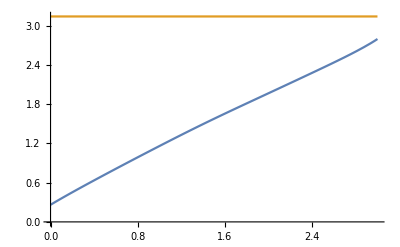

```mathematica
Plot[{geoθ[λ],π},{λ,λa,λb}]
```

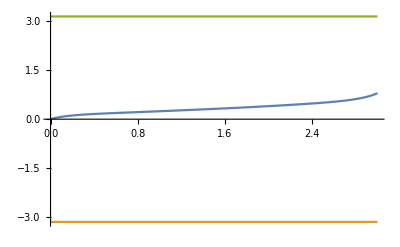

```mathematica
Plot[{geoϕ[λ],-π,π},{λ,λa,λb}]
```

```mathematica
λbp=2.99;
```

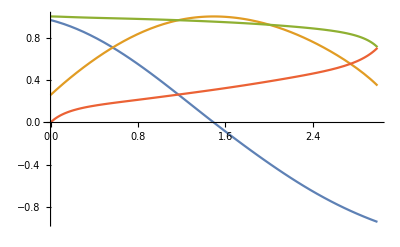

```mathematica
Plot[{Cos[geoθ[λ]],Sin[geoθ[λ]],Cos[geoϕ[λ]],Sin[geoϕ[λ]]},{λ,λa,λbp}]
```

```mathematica
dataGeoX=Flatten[Table[rFitLutetia[geoθ[λ],geoϕ[λ]]Sin[geoθ[λ]]Cos[geoϕ[λ]],{λ,λa,λbp,1/50}]];
dataGeoY=Flatten[Table[rFitLutetia[geoθ[λ],geoϕ[λ]]Sin[geoθ[λ]]Sin[geoϕ[λ]],{λ,λa,λbp,1/50}]];
dataGeoZ=Flatten[Table[rFitLutetia[geoθ[λ],geoϕ[λ]]Cos[geoθ[λ]],{λ,λa,λbp,1/50}]];
dataGeo=Transpose[{dataGeoX,dataGeoY,dataGeoZ}];
```

```mathematica
plotGeo=ListPointPlot3D[dataGeo,PlotStyle->Blue,Joined-> True]
```

ListPointPlot3D::nonopt: Options expected (instead of Joined) beyond position 1 in ListPointPlot3D[{{11.7112,0.,43.7068},{12.6574,0.23473,43.7494},{13.5955,0.470237,43.7724},{14.5271,0.706273,43.7757},«43»,{46.2816,11.0576,23.6752},{46.6843,11.2885,22.8746},{47.0732,11.5191,22.0673},«100»},PlotStyle→RGBColor[0, 0, 1],Joined]. An option must be a rule or a list of rules.

ListPointPlot3D[{{11.7112,0.,43.7068},{12.6574,0.23473,43.7494},{13.5955,0.470237,43.7724},{14.5271,0.706273,43.7757},{15.4532,0.94269,43.7591},{16.3744,1.17939,43.7224},{17.2911,1.41631,43.6653},{18.2033,1.65339,43.5874},{19.1112,1.89061,43.4885},{20.0144,2.12793,43.3682},{20.9128,2.36532,43.2263},{21.8061,2.60275,43.0625},{22.6937,2.84021,42.8766},{23.5753,3.07767,42.6683},{24.4503,3.31511,42.4374},{25.3182,3.5525,42.1838},{26.1783,3.78983,41.9074},{27.0301,4.02707,41.6082},{27.873,4.26421,41.2861},{28.7062,4.50123,40.9413},{29.5293,4.73812,40.5737},{30.3414,4.97485,40.1836},{31.1421,5.21142,39.7711},{31.9306,5.44781,39.3366},{32.7064,5.68401,38.8803},{33.4689,5.92002,38.4027},{34.2175,6.15583,37.9041},{34.9518,6.39142,37.385},{35.6714,6.62681,36.8459},{36.3757,6.86198,36.2874},{37.0644,7.09693,35.7102},{37.7372,7.33167,35.1147},{38.3938,7.56618,34.5017},{39.0341,7.80048,33.8718},{39.6578,8.03456,33.2258},{40.2648,8.26842,32.5644},{40.8552,8.50206,31.8882},{41.4289,8.73549,31.1979},{41.9859,8.96871,30.4944},{42.5265,9.20171,29.7783},{43.0506,9.4345,29.0503},{43.5586,9.66707,28.311},{44.0506,9.89942,27.5612},{44.527,10.1315,26.8014},{44.9879,10.3634,26.0324},{45.4338,10.5951,25.2547},{45.8649,10.8265,24.4688},{46.2816,11.0576,23.6752},{46.6843,11.2885,22.8746},{47.0732,11.5191,22.0673},{47.4489,11.7494,21.2539},{47.8116,11.9793,20.4346},{48.1617,12.2089,19.61},{48.4995,12.4382,18.7803},{48.8253,12.667,17.9459},{49.1394,12.8955,17.1071},{49.442,13.1234,16.2641},{49.7334,13.3509,15.4172},{50.0138,13.5779,14.5666},{50.2834,13.8043,13.7126},{50.5421,14.03,12.8552},{50.7902,14.2551,11.9946},{51.0277,14.4795,11.1311},{51.2545,14.7031,10.2646},{51.4706,14.9258,9.39543},{51.676,15.1475,8.52354},{51.8704,15.3682,7.64906},{52.0538,15.5878,6.77209},{52.2258,15.8061,5.8927},{52.3863,16.0231,5.01097},{52.535,16.2385,4.12699},{52.6715,16.4524,3.24083},{52.7954,16.6643,2.35258},{52.9065,16.8744,1.46233},{53.0043,17.0822,0.570199},{53.0883,17.2877,-0.323708},{53.1582,17.4905,-1.21926},{53.2133,17.6906,-2.11629},{53.2533,17.8875,-3.01466},{53.2777,18.0812,-3.91415},{53.2859,18.2712,-4.81456},{53.2774,18.4573,-5.71564},{53.2517,18.6391,-6.61714},{53.2082,18.8165,-7.51874},{53.1465,18.9889,-8.42012},{53.0661,19.1561,-9.32093},{52.9665,19.3177,-10.2208},{52.8471,19.4733,-11.1192},{52.7075,19.6226,-12.0157},{52.5473,19.7652,-12.9099},{52.366,19.9007,-13.8011},{52.1632,20.0286,-14.6889},{51.9386,20.1487,-15.5725},{51.6918,20.2604,-16.4514},{51.4226,20.3635,-17.3248},{51.1307,20.4574,-18.1921},{50.8158,20.5419,-19.0524},{50.4779,20.6166,-19.9051},{50.1168,20.6811,-20.7492},{49.7324,20.7351,-21.5841},{49.3248,20.7782,-22.4087},{48.894,20.8102,-23.2224},{48.4401,20.8308,-24.0241},{47.9633,20.8397,-24.813},{47.4638,20.8368,-25.5883},{46.9419,20.8219,-26.349},{46.398,20.7947,-27.0943},{45.8325,20.7553,-27.8233},{45.2458,20.7035,-28.5353},{44.6384,20.6392,-29.2294},{44.0109,20.5626,-29.9049},{43.3639,20.4736,-30.561},{42.6981,20.3723,-31.197},{42.0142,20.2588,-31.8123},{41.3128,20.1333,-32.4063},{40.5947,19.996,-32.9784},{39.8607,19.847,-33.5282},{39.1116,19.6867,-34.0552},{38.3481,19.5152,-34.559},{37.571,19.333,-35.0394},{36.7812,19.1402,-35.496},{35.9795,18.9374,-35.9287},{35.1665,18.7247,-36.3374},{34.3432,18.5026,-36.7218},{33.5102,18.2716,-37.0821},{32.6682,18.0318,-37.4182},{31.818,17.7838,-37.7302},{30.9602,17.528,-38.0181},{30.0954,17.2647,-38.2823},{29.2242,16.9943,-38.5229},{28.3472,16.7171,-38.7401},{27.4649,16.4336,-38.9342},{26.5777,16.1441,-39.1057},{25.686,15.8488,-39.2548},{24.7901,15.5482,-39.3819},{23.8903,15.2423,-39.4875},{22.9868,14.9315,-39.572},{22.0797,14.6159,-39.636},{21.169,14.2957,-39.6798},{20.2547,13.9708,-39.7041},{19.3364,13.6413,-39.7094},{18.414,13.307,-39.6963},{17.4869,12.9677,-39.6652},{16.5544,12.6229,-39.6167},{15.6156,12.2721,-39.5513},{14.6693,11.9144,-39.4696},{13.714,11.5485,-39.372},{12.7476,11.1729,-39.2587},{11.7676,10.7854,-39.1299},{10.7705,10.3826,-38.9855}},PlotStyle→RGBColor[0, 0, 1],Joined]

```mathematica
Show[{plot3DFitLutetia,plotGeo}]
```

-Graphics3D-

```mathematica
dataGeoFunction=Flatten[Map[ 100Abs[(√(geoFunction[#].geoFunction[#])-rFitLutetia[geoθ[#],geoθ[#]])/rFitLutetia[geoθ[#],geoθ[#]]]&,Range[10]/10]//N]
```

{0.642332,1.16655,1.74502,2.21956,2.40434,2.13311,1.31132,0.0347269,1.72936,3.45901}

```mathematica
plotErrL3=ListPlot[Transpose[{Range[dataErrorL3//Length],dataErrorL3}],PlotStyle->Red,AxesLabel->{Style["number\n of r",FontFamily->"Times",Medium],Style["100 |(r_fit-r)/r|",FontFamily->"Times",Medium]},PlotLegends->{Style["l_MAX=3",FontFamily->"Times"]}]
```

```mathematica
D[geoϕ[λ],λ]
```

{InterpolatingFunction[…][λ]}

Length of the geodesics

```mathematica
D[rFitLutetia[θ,ϕ],θ]
```

-2.20943 Cos[θ] Cos[ϕ]-2.90068 Cos[θ] Cos[2 ϕ] Sin[θ]+8.45496 Cos[θ] Cos[3 ϕ] Sin[θ]^2+2.96341 Cos[θ] Cos[5 ϕ] Sin[θ]^4+0.310776 Cos[θ] Sin[ϕ]+0.699265 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]+Cos[θ]^4 (-9.87472 Cos[θ] Cos[ϕ]+8.2629 Cos[θ] Sin[ϕ])+Cos[θ]^3 (5.70158 Cos[θ] Cos[ϕ]+15.3159 Cos[θ] Cos[2 ϕ] Sin[θ]-13.2674 Cos[θ] Sin[ϕ]+2.66407 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ])+0.285034 Cos[θ] Sin[θ]^2 Sin[3 ϕ]+Cos[θ] (-0.694913 Cos[θ] Cos[ϕ]-5.10528 Cos[θ] Cos[2 ϕ] Sin[θ]-10.2699 Cos[θ] Cos[3 ϕ] Sin[θ]^2+5.07658 Cos[θ] Sin[ϕ]-0.888025 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]-11.5092 Cos[θ] Sin[θ]^2 Sin[3 ϕ])+Cos[θ]^2 (17.8709 Cos[θ] Cos[ϕ]+20.3048 Cos[θ] Cos[2 ϕ] Sin[θ]+2.24319 Cos[θ] Cos[3 ϕ] Sin[θ]^2-2.18138 Cos[θ] Sin[ϕ]-4.89485 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]+20.8381 Cos[θ] Sin[θ]^2 Sin[3 ϕ])-4 Cos[θ]^3 Sin[θ] (4.81639-1.44256 Cos[4 ϕ]-9.87472 Cos[ϕ] Sin[θ]+8.2629 Sin[θ] Sin[ϕ]-0.710574 Sin[4 ϕ])-5 Cos[θ]^4 Sin[θ] (8.16283-1.85014 Cos[4 ϕ]-0.653604 Sin[4 ϕ])-Sin[θ] (-0.829469-1.85014 Cos[4 ϕ]-0.694913 Cos[ϕ] Sin[θ]-3.42329 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.25538-2.55264 Sin[θ]^2)-0.0449679 Cos[ϕ] Sin[ϕ]+5.07658 Sin[θ] Sin[ϕ]-0.444012 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[4 ϕ])-3 Cos[θ]^2 Sin[θ] (-3.8292+3.70028 Cos[4 ϕ]+5.70158 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.25538+7.65793 Sin[θ]^2)+0.0449679 Cos[ϕ] Sin[ϕ]-13.2674 Sin[θ] Sin[ϕ]+1.33204 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.30721 Sin[4 ϕ])-2 Cos[θ] Sin[θ] (-20.8444+2.88512 Cos[4 ϕ]+17.8709 Cos[ϕ] Sin[θ]+0.747729 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.548523+10.1524 Sin[θ]^2)-10.7925 Cos[ϕ] Sin[ϕ]-2.18138 Sin[θ] Sin[ϕ]-2.44743 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.94603 Sin[θ]^3 Sin[3 ϕ]+1.42115 Sin[4 ϕ])+5.86262 Cos[θ] Sin[θ]^4 Sin[5 ϕ]

```mathematica
D[rFitLutetia[θ,ϕ],ϕ]
```

10.7925 Cos[ϕ]^2-2.84229 Cos[4 ϕ]+0.310776 Cos[ϕ] Sin[θ]+0.349632 Cos[ϕ]^2 Sin[θ]^2+0.285034 Cos[3 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^5+2.20943 Sin[θ] Sin[ϕ]-10.7925 Sin[ϕ]^2-0.349632 Sin[θ]^2 Sin[ϕ]^2-2 (-0.548523-1.45034 Sin[θ]^2) Sin[2 ϕ]-8.45496 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (0.0449679 Cos[ϕ]^2+5.22883 Cos[4 ϕ]-13.2674 Cos[ϕ] Sin[θ]+1.33204 Cos[ϕ]^2 Sin[θ]^2-5.70158 Sin[θ] Sin[ϕ]-0.0449679 Sin[ϕ]^2-1.33204 Sin[θ]^2 Sin[ϕ]^2-2 (-1.25538+7.65793 Sin[θ]^2) Sin[2 ϕ]-14.8011 Sin[4 ϕ])+Cos[θ]^2 (-10.7925 Cos[ϕ]^2+5.68459 Cos[4 ϕ]-2.18138 Cos[ϕ] Sin[θ]-2.44743 Cos[ϕ]^2 Sin[θ]^2+20.8381 Cos[3 ϕ] Sin[θ]^3-17.8709 Sin[θ] Sin[ϕ]+10.7925 Sin[ϕ]^2+2.44743 Sin[θ]^2 Sin[ϕ]^2-2 (0.548523+10.1524 Sin[θ]^2) Sin[2 ϕ]-2.24319 Sin[θ]^3 Sin[3 ϕ]-11.5405 Sin[4 ϕ])+5.77024 Sin[4 ϕ]+Cos[θ]^4 (-2.84229 Cos[4 ϕ]+8.2629 Cos[ϕ] Sin[θ]+9.87472 Sin[θ] Sin[ϕ]+5.77024 Sin[4 ϕ])+Cos[θ]^5 (-2.61442 Cos[4 ϕ]+7.40056 Sin[4 ϕ])+Cos[θ] (-0.0449679 Cos[ϕ]^2-2.61442 Cos[4 ϕ]+5.07658 Cos[ϕ] Sin[θ]-0.444012 Cos[ϕ]^2 Sin[θ]^2-11.5092 Cos[3 ϕ] Sin[θ]^3+0.694913 Sin[θ] Sin[ϕ]+0.0449679 Sin[ϕ]^2+0.444012 Sin[θ]^2 Sin[ϕ]^2-2 (1.25538-2.55264 Sin[θ]^2) Sin[2 ϕ]+10.2699 Sin[θ]^3 Sin[3 ϕ]+7.40056 Sin[4 ϕ])-2.96341 Sin[θ]^5 Sin[5 ϕ]

```mathematica
drFitθ[θ_,ϕ_]:=-2.209429381828982 Cos[θ] Cos[ϕ]-2.90068478169439 Cos[θ] Cos[2 ϕ] Sin[θ]+8.454956353648155 Cos[θ] Cos[3 ϕ] Sin[θ]^2+2.9634075079232947 Cos[θ] Cos[5 ϕ] Sin[θ]^4+0.310776231872863 Cos[θ] Sin[ϕ]+0.6992646322380517 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]+Cos[θ]^4 (-9.87471576073588 Cos[θ] Cos[ϕ]+8.262904985870692 Cos[θ] Sin[ϕ])+Cos[θ]^3 (5.701583504162247 Cos[θ] Cos[ϕ]+15.315850945926108 Cos[θ] Cos[2 ϕ] Sin[θ]-13.26738416110994 Cos[θ] Sin[ϕ]+2.6640745391868963 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ])+0.2850337604530597 Cos[θ] Sin[θ]^2 Sin[3 ϕ]+Cos[θ] (-0.6949134283251226 Cos[θ] Cos[ϕ]-5.105283648642036 Cos[θ] Cos[2 ϕ] Sin[θ]-10.269879726807652 Cos[θ] Cos[3 ϕ] Sin[θ]^2+5.076578690838504 Cos[θ] Sin[ϕ]-0.8880248463956321 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]-11.509193228229947 Cos[θ] Sin[θ]^2 Sin[3 ϕ])+Cos[θ]^2 (17.870930309173815 Cos[θ] Cos[ϕ]+20.30479347186073 Cos[θ] Cos[2 ϕ] Sin[θ]+2.243187009488431 Cos[θ] Cos[3 ϕ] Sin[θ]^2-2.1813831855957346 Cos[θ] Sin[ϕ]-4.894852425666362 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]+20.83809098390399 Cos[θ] Sin[θ]^2 Sin[3 ϕ])-4 Cos[θ]^3 Sin[θ] (4.816394486903914-1.4425591445501287 Cos[4 ϕ]-9.87471576073588 Cos[ϕ] Sin[θ]+8.262904985870692 Sin[θ] Sin[ϕ]-0.7105735562332913 Sin[4 ϕ])-5 Cos[θ]^4 Sin[θ] (8.162834015917953-1.8501410274585612 Cos[4 ϕ]-0.6536043000716671 Sin[4 ϕ])-Sin[θ] (-0.8294685911214945-1.8501410274585612 Cos[4 ϕ]-0.6949134283251226 Cos[ϕ] Sin[θ]-3.4232932422692173 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (1.2553780488396649-2.552641824321018 Sin[θ]^2)-0.04496785438214449 Cos[ϕ] Sin[ϕ]+5.076578690838504 Sin[θ] Sin[ϕ]-0.44401242319781603 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.8363977427433156 Sin[θ]^3 Sin[3 ϕ]-0.6536043000716671 Sin[4 ϕ])-3 Cos[θ]^2 Sin[θ] (-3.829203361665252+3.7002820549171225 Cos[4 ϕ]+5.701583504162247 Cos[ϕ] Sin[θ]+Cos[2 ϕ] (-1.2553780488396649+7.657925472963054 Sin[θ]^2)+0.04496785438214449 Cos[ϕ] Sin[ϕ]-13.26738416110994 Sin[θ] Sin[ϕ]+1.3320372695934481 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+1.3072086001433343 Sin[4 ϕ])-2 Cos[θ] Sin[θ] (-20.84443005322268+2.8851182891002574 Cos[4 ϕ]+17.870930309173815 Cos[ϕ] Sin[θ]+0.7477290031628104 Cos[3 ϕ] Sin[θ]^3+Cos[2 ϕ] (0.5485234942542312+10.152396735930365 Sin[θ]^2)-10.792514116115738 Cos[ϕ] Sin[ϕ]-2.1813831855957346 Sin[θ] Sin[ϕ]-2.447426212833181 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+6.946030327967996 Sin[θ]^3 Sin[3 ϕ]+1.4211471124665827 Sin[4 ϕ])+5.862623169975167 Cos[θ] Sin[θ]^4 Sin[5 ϕ]
```

```mathematica
drFitϕ[θ_,ϕ_]:=10.792514116115738 Cos[ϕ]^2-2.8422942249331653 Cos[4 ϕ]+0.310776231872863 Cos[ϕ] Sin[θ]+0.34963231611902584 Cos[ϕ]^2 Sin[θ]^2+0.2850337604530597 Cos[3 ϕ] Sin[θ]^3+5.862623169975167 Cos[5 ϕ] Sin[θ]^5+2.209429381828982 Sin[θ] Sin[ϕ]-10.792514116115738 Sin[ϕ]^2-0.34963231611902584 Sin[θ]^2 Sin[ϕ]^2-2 (-0.5485234942542312-1.450342390847195 Sin[θ]^2) Sin[2 ϕ]-8.454956353648155 Sin[θ]^3 Sin[3 ϕ]+Cos[θ]^3 (0.04496785438214449 Cos[ϕ]^2+5.228834400573337 Cos[4 ϕ]-13.26738416110994 Cos[ϕ] Sin[θ]+1.3320372695934481 Cos[ϕ]^2 Sin[θ]^2-5.701583504162247 Sin[θ] Sin[ϕ]-0.04496785438214449 Sin[ϕ]^2-1.3320372695934481 Sin[θ]^2 Sin[ϕ]^2-2 (-1.2553780488396649+7.657925472963054 Sin[θ]^2) Sin[2 ϕ]-14.80112821966849 Sin[4 ϕ])+Cos[θ]^2 (-10.792514116115738 Cos[ϕ]^2+5.684588449866331 Cos[4 ϕ]-2.1813831855957346 Cos[ϕ] Sin[θ]-2.447426212833181 Cos[ϕ]^2 Sin[θ]^2+20.83809098390399 Cos[3 ϕ] Sin[θ]^3-17.870930309173815 Sin[θ] Sin[ϕ]+10.792514116115738 Sin[ϕ]^2+2.447426212833181 Sin[θ]^2 Sin[ϕ]^2-2 (0.5485234942542312+10.152396735930365 Sin[θ]^2) Sin[2 ϕ]-2.243187009488431 Sin[θ]^3 Sin[3 ϕ]-11.54047315640103 Sin[4 ϕ])+5.770236578200515 Sin[4 ϕ]+Cos[θ]^4 (-2.8422942249331653 Cos[4 ϕ]+8.262904985870692 Cos[ϕ] Sin[θ]+9.87471576073588 Sin[θ] Sin[ϕ]+5.770236578200515 Sin[4 ϕ])+Cos[θ]^5 (-2.6144172002866686 Cos[4 ϕ]+7.400564109834245 Sin[4 ϕ])+Cos[θ] (-0.04496785438214449 Cos[ϕ]^2-2.6144172002866686 Cos[4 ϕ]+5.076578690838504 Cos[ϕ] Sin[θ]-0.44401242319781603 Cos[ϕ]^2 Sin[θ]^2-11.509193228229947 Cos[3 ϕ] Sin[θ]^3+0.6949134283251226 Sin[θ] Sin[ϕ]+0.04496785438214449 Sin[ϕ]^2+0.44401242319781603 Sin[θ]^2 Sin[ϕ]^2-2 (1.2553780488396649-2.552641824321018 Sin[θ]^2) Sin[2 ϕ]+10.269879726807652 Sin[θ]^3 Sin[3 ϕ]+7.400564109834245 Sin[4 ϕ])-2.9634075079232947 Sin[θ]^5 Sin[5 ϕ]
```

```mathematica
drFitϕ[θ,ϕ]
```

```mathematica
dgeoθ[λ_]:=D[geoθ[λ],λ]
D[geoϕ[λ],λ]
```

```mathematica
geods[λ_]:=√((rFitLutetia[θ,ϕ]^2+drFitθ[θ,ϕ]^2)D[geoθ[λ],λ]^2+(rFitLutetia[θ,ϕ]^2 Sin[θ]^2+drFitϕ[θ,ϕ]^2)D[geoϕ[λ],λ]^2+2drFitϕ[θ,ϕ]drFitθ[θ,ϕ]D[geoθ[λ],λ]D[geoϕ[λ],λ])
```

```mathematica
NIntegrate[geods[λ],{λ,λa,λbp}]
```

```mathematica
First@Sin[geoθ[λ]]
```

Sin[InterpolatingFunction[…][λ]]

```mathematica
First@rFitLutetia[geoθ[λ],geoϕ[λ]]{First@Sin[geoθ[λ]]First@Cos[geoϕ[λ]],First@Sin[geoθ[λ]]First@Sin[geoϕ[λ]],First@Cos[geoθ[λ]]}
```

54.3486-1.44256 Cos[4 InterpolatingFunction[…][λ]]+10.7925 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]+Cos[InterpolatingFunction[…][λ]]^5 (8.16283-1.85014 Cos[4 InterpolatingFunction[…][λ]]-0.653604 Sin[4 InterpolatingFunction[…][λ]])-0.710574 Sin[4 InterpolatingFunction[…][λ]]-2.20943 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]+0.310776 Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]+0.349632 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^2+2.81832 Cos[3 InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^3+0.0950113 Sin[3 InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^3+0.592682 Cos[5 InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^5+1.17252 Sin[5 InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^5+Cos[InterpolatingFunction[…][λ]]^4 (4.81639-1.44256 Cos[4 InterpolatingFunction[…][λ]]-0.710574 Sin[4 InterpolatingFunction[…][λ]]-9.87472 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]+8.2629 Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]])+Cos[2 InterpolatingFunction[…][λ]] (-0.548523-1.45034 Sin[InterpolatingFunction[…][λ]]^2)+Cos[InterpolatingFunction[…][λ]] (-0.829469-1.85014 Cos[4 InterpolatingFunction[…][λ]]-0.0449679 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]-0.653604 Sin[4 InterpolatingFunction[…][λ]]-0.694913 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]+5.07658 Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]-0.444012 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^2-3.42329 Cos[3 InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^3-3.8364 Sin[3 InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^3+Cos[2 InterpolatingFunction[…][λ]] (1.25538-2.55264 Sin[InterpolatingFunction[…][λ]]^2))+Cos[InterpolatingFunction[…][λ]]^3 (-3.8292+3.70028 Cos[4 InterpolatingFunction[…][λ]]+0.0449679 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]+1.30721 Sin[4 InterpolatingFunction[…][λ]]+5.70158 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]-13.2674 Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]+1.33204 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^2+Cos[2 InterpolatingFunction[…][λ]] (-1.25538+7.65793 Sin[InterpolatingFunction[…][λ]]^2))+Cos[InterpolatingFunction[…][λ]]^2 (-20.8444+2.88512 Cos[4 InterpolatingFunction[…][λ]]-10.7925 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]+1.42115 Sin[4 InterpolatingFunction[…][λ]]+17.8709 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]-2.18138 Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]-2.44743 Cos[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^2+0.747729 Cos[3 InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^3+6.94603 Sin[3 InterpolatingFunction[…][λ]] Sin[InterpolatingFunction[…][λ]]^3+Cos[2 InterpolatingFunction[…][λ]] (0.548523+10.1524 Sin[InterpolatingFunction[…][λ]]^2))

```mathematica
geoFunction[λ_]:=Evaluate[First@rFitLutetia[geoθ[λ],geoϕ[λ]]{First@Sin[geoθ[λ]]First@Cos[geoϕ[λ]],First@Sin[geoθ[λ]]First@Sin[geoϕ[λ]],First@Cos[geoθ[λ]]}]
```

```mathematica
First@rFitLutetia[geoθ[λ],geoϕ[λ]]{First@Sin[geoθ[λ]]First@Cos[geoϕ[λ]],First@Sin[geoθ[λ]]First@Sin[geoϕ[λ]],First@Cos[geoθ[λ]]}/.λ->(.081)/10//N
```

{Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] (54.3486-1.44256 Cos[4. InterpolatingFunction[…][0.1 .081]]+10.7925 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+Cos[InterpolatingFunction[…][0.1 .081]]^5 (8.16283-1.85014 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.653604 Sin[4. InterpolatingFunction[…][0.1 .081]])-0.710574 Sin[4. InterpolatingFunction[…][0.1 .081]]-2.20943 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+0.310776 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+0.349632 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+2.81832 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+0.0950113 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+0.592682 Cos[5. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^5+1.17252 Sin[5. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^5+Cos[InterpolatingFunction[…][0.1 .081]]^4 (4.81639-1.44256 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.710574 Sin[4. InterpolatingFunction[…][0.1 .081]]-9.87472 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+8.2629 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]])+Cos[2. InterpolatingFunction[…][0.1 .081]] (-0.548523-1.45034 Sin[InterpolatingFunction[…][0.1 .081]]^2)+Cos[InterpolatingFunction[…][0.1 .081]] (-0.829469-1.85014 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.0449679 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-0.653604 Sin[4. InterpolatingFunction[…][0.1 .081]]-0.694913 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+5.07658 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-0.444012 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2-3.42329 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3-3.8364 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+Cos[2. InterpolatingFunction[…][0.1 .081]] (1.25538-2.55264 Sin[InterpolatingFunction[…][0.1 .081]]^2))+Cos[InterpolatingFunction[…][0.1 .081]]^3 (-3.8292+3.70028 Cos[4. InterpolatingFunction[…][0.1 .081]]+0.0449679 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.30721 Sin[4. InterpolatingFunction[…][0.1 .081]]+5.70158 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-13.2674 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.33204 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+Cos[2. InterpolatingFunction[…][0.1 .081]] (-1.25538+7.65793 Sin[InterpolatingFunction[…][0.1 .081]]^2))+Cos[InterpolatingFunction[…][0.1 .081]]^2 (-20.8444+2.88512 Cos[4. InterpolatingFunction[…][0.1 .081]]-10.7925 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.42115 Sin[4. InterpolatingFunction[…][0.1 .081]]+17.8709 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-2.18138 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-2.44743 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+0.747729 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+6.94603 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+Cos[2. InterpolatingFunction[…][0.1 .081]] (0.548523+10.1524 Sin[InterpolatingFunction[…][0.1 .081]]^2))),Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] (54.3486-1.44256 Cos[4. InterpolatingFunction[…][0.1 .081]]+10.7925 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+Cos[InterpolatingFunction[…][0.1 .081]]^5 (8.16283-1.85014 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.653604 Sin[4. InterpolatingFunction[…][0.1 .081]])-0.710574 Sin[4. InterpolatingFunction[…][0.1 .081]]-2.20943 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+0.310776 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+0.349632 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+2.81832 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+0.0950113 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+0.592682 Cos[5. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^5+1.17252 Sin[5. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^5+Cos[InterpolatingFunction[…][0.1 .081]]^4 (4.81639-1.44256 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.710574 Sin[4. InterpolatingFunction[…][0.1 .081]]-9.87472 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+8.2629 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]])+Cos[2. InterpolatingFunction[…][0.1 .081]] (-0.548523-1.45034 Sin[InterpolatingFunction[…][0.1 .081]]^2)+Cos[InterpolatingFunction[…][0.1 .081]] (-0.829469-1.85014 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.0449679 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-0.653604 Sin[4. InterpolatingFunction[…][0.1 .081]]-0.694913 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+5.07658 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-0.444012 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2-3.42329 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3-3.8364 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+Cos[2. InterpolatingFunction[…][0.1 .081]] (1.25538-2.55264 Sin[InterpolatingFunction[…][0.1 .081]]^2))+Cos[InterpolatingFunction[…][0.1 .081]]^3 (-3.8292+3.70028 Cos[4. InterpolatingFunction[…][0.1 .081]]+0.0449679 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.30721 Sin[4. InterpolatingFunction[…][0.1 .081]]+5.70158 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-13.2674 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.33204 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+Cos[2. InterpolatingFunction[…][0.1 .081]] (-1.25538+7.65793 Sin[InterpolatingFunction[…][0.1 .081]]^2))+Cos[InterpolatingFunction[…][0.1 .081]]^2 (-20.8444+2.88512 Cos[4. InterpolatingFunction[…][0.1 .081]]-10.7925 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.42115 Sin[4. InterpolatingFunction[…][0.1 .081]]+17.8709 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-2.18138 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-2.44743 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+0.747729 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+6.94603 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+Cos[2. InterpolatingFunction[…][0.1 .081]] (0.548523+10.1524 Sin[InterpolatingFunction[…][0.1 .081]]^2))),Cos[InterpolatingFunction[…][0.1 .081]] (54.3486-1.44256 Cos[4. InterpolatingFunction[…][0.1 .081]]+10.7925 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+Cos[InterpolatingFunction[…][0.1 .081]]^5 (8.16283-1.85014 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.653604 Sin[4. InterpolatingFunction[…][0.1 .081]])-0.710574 Sin[4. InterpolatingFunction[…][0.1 .081]]-2.20943 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+0.310776 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+0.349632 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+2.81832 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+0.0950113 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+0.592682 Cos[5. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^5+1.17252 Sin[5. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^5+Cos[InterpolatingFunction[…][0.1 .081]]^4 (4.81639-1.44256 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.710574 Sin[4. InterpolatingFunction[…][0.1 .081]]-9.87472 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+8.2629 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]])+Cos[2. InterpolatingFunction[…][0.1 .081]] (-0.548523-1.45034 Sin[InterpolatingFunction[…][0.1 .081]]^2)+Cos[InterpolatingFunction[…][0.1 .081]] (-0.829469-1.85014 Cos[4. InterpolatingFunction[…][0.1 .081]]-0.0449679 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-0.653604 Sin[4. InterpolatingFunction[…][0.1 .081]]-0.694913 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+5.07658 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-0.444012 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2-3.42329 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3-3.8364 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+Cos[2. InterpolatingFunction[…][0.1 .081]] (1.25538-2.55264 Sin[InterpolatingFunction[…][0.1 .081]]^2))+Cos[InterpolatingFunction[…][0.1 .081]]^3 (-3.8292+3.70028 Cos[4. InterpolatingFunction[…][0.1 .081]]+0.0449679 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.30721 Sin[4. InterpolatingFunction[…][0.1 .081]]+5.70158 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-13.2674 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.33204 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+Cos[2. InterpolatingFunction[…][0.1 .081]] (-1.25538+7.65793 Sin[InterpolatingFunction[…][0.1 .081]]^2))+Cos[InterpolatingFunction[…][0.1 .081]]^2 (-20.8444+2.88512 Cos[4. InterpolatingFunction[…][0.1 .081]]-10.7925 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]+1.42115 Sin[4. InterpolatingFunction[…][0.1 .081]]+17.8709 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-2.18138 Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]-2.44743 Cos[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^2+0.747729 Cos[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+6.94603 Sin[3. InterpolatingFunction[…][0.1 .081]] Sin[InterpolatingFunction[…][0.1 .081]]^3+Cos[2. InterpolatingFunction[…][0.1 .081]] (0.548523+10.1524 Sin[InterpolatingFunction[…][0.1 .081]]^2)))}

```mathematica
geoFunction[1/10]//N
```

{16.3744,1.17939,43.7224}

```mathematica
plotGeoFunction=ParametricPlot3D[geoFunction[λ],{λ,0,2.99},PlotStyle->{Blue,Thick}]
```

-Graphics3D-

```mathematica
plotLutetiaTransparent=SphericalPlot3D[rFitLutetia[θ,ϕ],{θ,0,π},{ϕ,-π,π},PlotStyle->{Transparent}(*Epilog->{PointSize[Medium],Line[dataGeo]}*)]
```

-Graphics3D-

```mathematica
Show[{plotLutetiaTransparent,plotGeoFunction}]
```

-Graphics3D-